### Summary of the simulation

The simulation generates the ancestral recombination graph, by tracking the ancestors of a sample of genomes back through time, until all ancestral genomes are ancestors to the whole sample.  The simulation can be conditional on a selective sweep, which is defined by the numbers of copies of the favourable allele in the population.  A Wright-Fisher model with constant populations size 2N haploid genomes is assumed. A region of genome of map length R is followed, with the selected locus at the leftmost point (i.e., at 0). For simplicity, we allow at most one crossover, with probability R; we simulate R<<1, so this is close to the case with no interference between crossovers. Once the ARG is constructed, genealogies along the genome can be constructed, and their branches identified. Neutral SNP can be added, assuming infinite-sites mutation; each SNP is associated with a branch in the ARG.

Each ancestor is represented by three elements: its genotype at the selected locus; a list of  junctions, and a list of the sampled genomes that descend from each interval.  For example, {0,{0.02,0.035},{{1,3},{},{5,6,7}}} represents a genome divided into three regions {0,0.02}, {0.02,0.03}, {0.035,R}, which are ancestral to sampled genomes {1,3},{},{5,6,7}, respectively; the selected locus at position 0 carries allele 0.  For the neutral case, we simply set this genotype to 0 throughout.

In the sampled generation, a sample of k genomes is represented as {{0,{},{{1}}},…,{0,{},{{k}}}: the j'th genome is ancestral to itself, (j), over its whole length.  Stepping back, crossovers are generated for each genome, drawn from a Poisson with expectation R, and uniformly distributed.  To be efficient, these are generated in a single draw.  Genomes that experienced a crossover are replaced by two parent genomes. For example, if there were a crossover at j_1,  {0,{},{1}} would be replaced by genomes {0,{j_1},{{1},{}}} and {X,{j_1},{{},{1}}}.  Here, the genotype X is chosen randomly with probability equal to the allele frequency in the whole population.  Stepping back in time, coalescence is simulated by assigning each genome a parent with the same allelic state. If the population in the previous generation carries k copies with allele X=1, then each current genome is assigned a random integer in {1,k}, and similarly for allele X=0. Parent genomes are then assigned by merging ancestries. For example, if current genomes {0,{j_1},{{1},{}}} and {0,{j_2},{{3},{2,3}}} share a parent, and j_1<j_2, then that parent is assigned as {0, {j_1, j_2}, {{1, 3}, {3}, {2,3}}}. Note that coalescence can only occur within a genetic background (defined by X=0 or 1), and that multiple coalescences between multiple  genomes can occur: we simulate the Wright-Fisher model, not the standard coalescent, which only applies in the limit of a large population.  This is important, since in the early stages of a sweep, the new allele is present in few copies.  In each generation, the list of ancestral genomes is tidied by deleting genomes that are not ancestral to the sample, and deleting junctions that separate regions with the same ancestry.  The algorithm is iterated back, until every ancestor is ancestral to the whole sample, which implies that all genealogies have reached their single common ancestor.

Very large populations can be simulated, since we only track ancestors. The computation is limited by the number of ancestors, which increases with 2 N_e R, and the time to complete coalescence, whioch increases with 4 N_e.   For a given 2 N_e R, it is most efficient to choose a modest N_e and a large R, but N_e should not be so small that results deviate from the standard coalescent. This can be determined by making some runs for larger N_e, and by checking against theoretical predictions for the standard coalescent.

In the neutral case, the allelic state is simply set to X=0.  To simulate conditional on a sweep, the trajectory is first generated, by simulating forwards from a single mutation, according to the Wright-Fisher model, and conditioning on fixation.  The trajectory is then augmented back in time, by setting it at one copy into the indefinite past.  (It is not obvious what the correct choice should be here, but since the genealogy at the selected locus must have coalesced completely at the time of the sweep, and since linked lineages are unlikely to coalesce into the ancestor of the mutation (assumed to be in a single copy) the choice should not make much difference). By first drawing the trajectory, and then simulating coalescence and recombination conditional on it, we can separate random variation in the trajectory, from random variation in the outcome for a given trajectory.  We can only infer properties of the single actual trajectory, which may well deviate substantially from expectation.

The core structure, which defines the ARG, is the list of ancestors, traced back through time.  From this, we generate a list of all distinct junctions, and thus, of all intervals along the genome; for each of these, a genealogy is constructed.  We then construct a list of branches, each branch being generated by a coalescence event that occurs at a specific time, and that brings together a specific set of sampled genomes.   For each branch, we list the regions of genome that it covers, in which generation, in the form {{t,{{r_0,r_1},…}},…}; note that regions may be disjunct.  The full list of branches covers the whole ancestry.

Neutral SNP are generated, assuming infinite-sites mutation.  For every branch, SNP are generated with density μ/r per map length; these are then combined into a list of SNP, each defined by its time of origin, its map position, and its branch, {t,x,b}.   In practice, of course, we must infer branches from the SNP that they carry.

#### Notes on executing the code

To execute the examples here, initialise the accompanying package GenealogiesNewV5 as well as this notebook; this sets up definitions for handling genealogies.

This notebook is large, but could be reduced by deleting graphics, or converting them to bitmap.

Data from specific examples in the paper are stored as Mathematica definitions:
	Neutral example: ”pl10 31 Oct”, “snp10full 3 Dec”
	Sweep example:  “Big sweeps s=0.1, 2N=400 R=0.2 20 genomes 2 Jan”
For the sweep example, replicate genealogies were generated, and stored in “Big sweeps s=0.1, 2N=400 R=0.2 20 genomes reps 4 Jan”. This is not provided, since it is enormous (3.9Gb). However, replicates conditional on the given sweep can be generated quickly.
Make sure to use SetDirectory to specify where these are stored on your machine.

## Neutral case

### Example with 10 genomes, sampled from 2N=100 on R=0.1 (i.e. 10cM); SNP generated with μ/r=2

#### Setting up, and saving results

This is very fast. It takes 268 generations until complete coalescence:

```mathematica
Timing[time=0;pl10=makeC[10,0.1,100];Length[pl10]]
```

{0.377784,269}

The simulation stores individuals that are represented as {X,{r_(1,2),…},{a_1.,a_2,…}}, where X is the genotype at the selected locus,  {r_(1,2),…} lists the breakpoints, and {S_1.,S_2,…} lists the sets of sampled genomes that each interval is ancestral to.  The list below goves the lengths of these sets, for individuals 10 generations from the end, when there are  8 ancestral genomes, and much of the genome has coalesced (represented by sets S of length 10).

```mathematica
Map[Length,pl10[[-10,All,3]],{2}]
```

{{0,3,0,6,10,0,10,0},{0,10},{0,10,0},{0,10,0},{0,10,7,10,0,10,4,0},{0,10,0},{10,0},{0,10,0}}

The # of  genomes that carry any ancestral material drops rapidly at t=100, but then increases.  The number of ancestral lineages would keep fluctuating even after full coalescence.

```mathematica
ListLinePlot[Length/@pl10,PlotRange->{{1,300},{1,10}},PlotStyle->PointSize[0.01]]
```

-Graphics-

This saves the simulated ancestry (pl10)

```mathematica
Save["pl10 31 Oct",pl10];
```

This reads the data back in, to recover this example.

```mathematica
<<"pl10 31 Oct";
```

#### Notes on definition of branches

Initially, branches were defined by their descendant genomes. However, this may conflate branches that bring together the same lineages via different coalescence events.  The simplest solution is to also require distinct branches to be generated at different times.  There is still the possibility that two coalescence events occur in the same generation and bring together the same lineages, but this seems very unlikely; it is not clear how to tag coalescence events to avoid this.

New functions are defined with the suffix ... Full that distinguish blocks that originate at different times, t. branchListFull returns branches in the form {S,t, {{r_1,r_2},…}}, allowing for the possibility that they may fall in multiple intervals (though this does not happen in this example).  posBlockFull[pop,{S,t,{{r_1,r_2},…}],R] returns the instances of the branch in the form {t,{r_1,r_2}}.  These ..Full versions should be used throughout.

#### Making the genealogies

This sets up a list of the 34 genealogies along the 10cM stretch of genome:

```mathematica
Timing[gl10=makeGenealogy[pl10,#,0.1]&/@intervals[pl10,0.1];]
```

{2.04559,Null}

These are the 34 non-recombined intervals:

```mathematica
intervals[pl10,0.1]//TableForm
```

0 | 0.000485901
0.000485901 | 0.00215397
0.00215397 | 0.00269484
0.00269484 | 0.00368421
0.00368421 | 0.00868471
0.00868471 | 0.00912131
0.00912131 | 0.0140003
0.0140003 | 0.015999
0.015999 | 0.0184439
0.0184439 | 0.0189914
0.0189914 | 0.0193689
0.0193689 | 0.021544
0.021544 | 0.0216572
0.0216572 | 0.0253309
0.0253309 | 0.0446031
0.0446031 | 0.0453142
0.0453142 | 0.0494893
0.0494893 | 0.0497073
0.0497073 | 0.0505236
0.0505236 | 0.050558
0.050558 | 0.0607542
0.0607542 | 0.0615051
0.0615051 | 0.0625631
0.0625631 | 0.0631933
0.0631933 | 0.0712151
0.0712151 | 0.0735098
0.0735098 | 0.0745833
0.0745833 | 0.074802
0.074802 | 0.0779924
0.0779924 | 0.0786718
0.0786718 | 0.0826169
0.0826169 | 0.0965451
0.0965451 | 0.0991522
0.0991522 | 0.1

This is a movie of the genealogies along the genome.  Numbers label the branches, and the vertical scale is proportional to coalescence times. The vertical axis is always 270 (the time for all of the genome to coalesce.

```mathematica
ListAnimate[Show[PlotGenealogy[#,NodeFunction->plotCoords[1]],PlotRange->{{0,11},{0,270}},AspectRatio->0.7]&/@gl10]
```

There are 34 intervals, 24 distinct genealogies, and 15 distinct topologies:

```mathematica
Length/@{gl10,Union[gl10],Union[gl10/.{{_Integer,{}}->{τ,{}}}]}
```

{34,24,15}

#### Throwing down SNP: μ/r=2

This sets up a list of the branches (branchList); generates SNP, listing them as {t,x,k} for branch #k (makeSNP), and throws them onto the 100 genomes (addSNP):

```mathematica
blf10=branchListFull[pl10,0.1];
snp10full=makeSNP[posBlockFull[pl10,#,0.1],2]&/@blf10;
pop10full=addSNP[blf10,snp10full];
```

This saves this set of SNP; the specific example used can be recovered using <<“snp10full 3 Dec”

```mathematica
Save["snp10full 4 Dec",snp10full];
```

```mathematica
<<"snp10full 3 Dec";
```

There are 87 SNP on 34 intervals. Each SNP is represented on average 254/87 times:

```mathematica
{Length/@{Flatten[pop10full,1],Union[Flatten[pop10full,1]]},Length[intervals[pl10,0.1]]}
```

{{254,87},34}

This is the SFS:

{{1,33},{2,13},{3,8},{4,16},{5,5},{6,5},{7,5},{8,1},{9,1}}

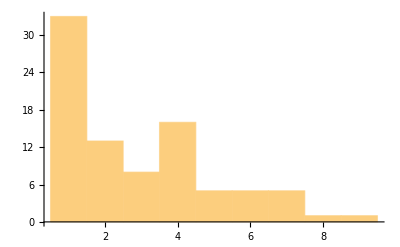

```mathematica
sfs=Last/@Tally[Flatten[pop10full,1]];
Tally[sfs]//Sort
Histogram[sfs]
```

#### Finding the 9 branches with ≥4 SNP

There are 87 SNP on 54 branches, of which 53 are on the  9 branches that have ≥4 SNP:

```mathematica
big2full=Pick[Range[Length[blf10]],(Length[#]≥4)&/@snp10full];
{{Length[blf10],Length[big2full]},
{Total[Length/@snp10full],Total[Length/@snp10full[[big2full]]]}}//TableForm
```

54 | 9
87 | 53

These are the index; the # SNP (up to 10); the timespan; and the width on the map. There is an inverse relation between map length and timespan for these 9 longest branches

```mathematica
tt={big2full,Length/@snp10full[[big2full]],branchLength[posBlockFull[pl10,#,0.1]]&/@blf10[[big2full]],branchWidth[posBlockFull[pl10,#,0.1]]&/@blf10[[big2full]]};
tt//TableForm
```

1 | 3 | 4 | 9 | 17 | 25 | 28 | 44 | 50
10 | 4 | 4 | 8 | 6 | 4 | 9 | 4 | 4
64 | 64 | 7 | 184 | 183 | 49 | 248 | 68 | 204
0.0637979 | 0.0180866 | 0.0984601 | 0.0107261 | 0.00815806 | 0.0240657 | 0.00920392 | 0.0188954 | 0.0123583

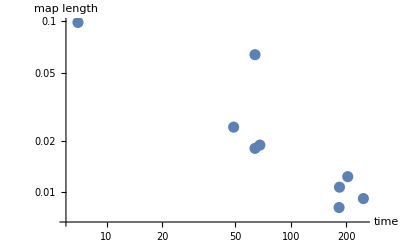

-0.870116-0.690694 t

```mathematica
ListLogLogPlot[Flatten/@tt⟦{3,4}⟧//Transpose,PlotStyle->PointSize[0.02],PlotRange->All,AxesLabel->{"time","map\nlength"}]
Fit[Log[Flatten/@tt⟦{3,4}⟧//Transpose],{1,t},t]
```

#### inverse relation between block length and timespan

This was generated from a different example, in which all 100 genomes were sampled. It is included to support the argument that, because the slope of the relation between map length and time span is weaker than inverse (i.e. slope > -1), deep branches will tend to have a larger area and carry more SNP.

This generates a table txal of the time spanned by the branch; the mean map length covered by it (averaged over generations); and its area (which determines the expected # of SNP that it carries). txalm takes the mean values, when branches are grouped by timespan.

```mathematica
<<"pl2 27 Oct";
tb=branchListFull[pl2,0.1];
txal=(pb=posBlockFull[pl2,#,0.1];
{Length[Union[pb⟦All,1⟧]],Mean[pb⟦All,2⟧.{-1,1}],Total[pb⟦All,2⟧.{-1,1}]})&/@tb;
txalm=Mean/@GatherBy[txal,Log[#⟦1⟧]&];
```

It is not obvious which direction causality runs, and so we plot map length against the time spanned by the branch (left) as well as time span against map length (right).  The 482 branches are shown by blue dots, and the mean for each timespan is shown by the red dots.  The two fits (top, bottom row in the table)  are to the blue vs the red dots. In each plot, the black line is ~t^-1, to indicate the slope expected with a simple inverse relation.  There is an inverse relation, but the least-squares fit is x~t^-0.68(left), or t~x^-0.54rather than the expected simple inverse.

Here, the exponent has magnitude less than 1 due to regression to the mean. Suppose that we have two variables, log(t)=y+v_t and log(x)=1/y+v_x, which are determined by an underlying inverse relationship plus independent random errors with variances v_t, v_x, then the regression coefficient of log(x) on log(t) is -v_y/(v_t+v_y), and of log(t) on log(x) is -v_y/(v_x+v_y) - both of which have magnitude less than 1.

```mathematica
GraphicsRow[{Show[ListLogLogPlot[txal[[All,{1,2}]]],ListLogLogPlot[txalm[[All,{1,2}]],PlotStyle->Red],LogLogPlot[0.3 t^-1,{t,1,500},PlotStyle->Black],
AxesLabel->{"time\nspan","map\nlength"}],
Show[ListLogLogPlot[Reverse/@txal[[All,{1,2}]]],ListLogLogPlot[Reverse/@txalm[[All,{1,2}]],PlotStyle->Red],LogLogPlot[0.4 x^-1,{x,10^-4,0.1},PlotStyle->Black],AxesLabel->{"map\nlength","time\nspan"}]}]
{{Fit[Log[txal[[All,{1,2}]]],{1,t},t],Fit[Log[txalm[[All,{1,2}]]],{1,t},t]},
{Fit[Log[Reverse/@txal[[All,{1,2}]]],{1,r},r],Fit[Log[Reverse/@txalm[[All,{1,2}]]],{1,r},r]}}//Transpose//TableForm
```

-Graphics-

-3.16957-0.681402 t | -0.465778-0.542427 r
-2.62644-0.656533 t | -0.00112289-0.739972 r

The key question is, what kind of branches carry the total ancestry (measured by the area of the branch, and proportional to the expected # of SNP). The area of a branch increases with its timespan (as ~t^0.34), and with the map length that it spans.

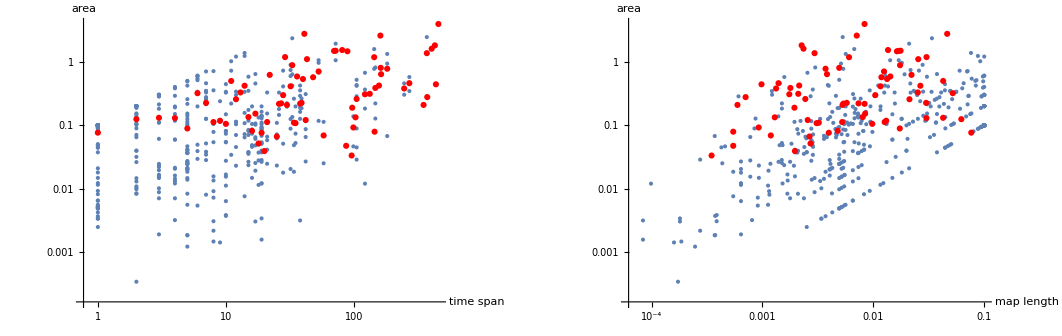

-3.17497+0.342694 t | 2.91104+0.369998 r
0.124608+0.262843 t | -4.68366+0.347307 r

```mathematica
GraphicsRow[{Show[ListLogLogPlot[txal[[All,{1,3}]]],ListLogLogPlot[txalm[[All,{1,3}]],PlotStyle->Red],
AxesLabel->{"time\nspan","area"}],
Show[ListLogLogPlot[txal[[All,{2,3}]]],ListLogLogPlot[txalm[[All,{2,3}]],PlotStyle->Red],AxesLabel->{"map\nlength","area"}]}]
{{Fit[Log[txal[[All,{1,3}]]],{1,t},t],Fit[Log[txalm[[All,{2,3}]]],{1,t},t]},
{Fit[Log[Reverse/@txal[[All,{1,3}]]],{1,r},r],Fit[Log[Reverse/@txalm[[All,{2,3}]]],{1,r},r]}}//Transpose//TableForm
```

The left plot shows the distribution of areas; note the peaks at 0.1, 0.2 which correspond to branches that start at the tips and go back 1 or 2 generations before the first coalescence. The  right plot shows the cumulative distribution of area. The total ancestry (map length*generations) is 105.3, on 488 branches; 44 branches with area>0.58  carry half of this, and 243 with area>0.1 carry 90% of the total ancestry.

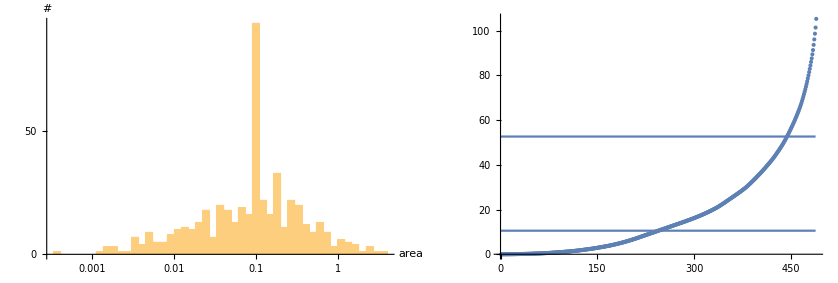

| 50% | 90%
488 | 44 | 243
105.298 | 0.578474 | 0.1

```mathematica
sa=Sort[txal[[All,3]]];ta=FoldList[Plus,0,sa];
nb=Length[txal];n50=nb-findT[ta,Last[ta]/2];n90=nb-findT[ta,Last[ta]/10];
GraphicsRow[{Histogram[Log[txal[[All,3]]],40,Ticks->{{{Log[0.001],"0.001"},{Log[0.01],"0.01"},{Log[0.1],"0.1"},{Log[1],"1"}},{0,50,100}},AxesLabel->{"area","#"}],
Show[ListPlot[ta,PlotRange->All],Plot[Last[ta]{1/2,1/10},{x,0,488}]]}]
{{"","50%","90%"},{nb,n50,n90},{Last[ta],sa[[-n50]],sa[[-n90]]}}//TableForm
```

Histograms of time span (left) and map length (right). Blue: all 488 branches; yellow: the 243 branches that carry 90% of the ancestry; red: the 44 branches that carry 50% of the ancestry. The 44 most substantial branches (red) span a wide range, but tend to have longer timespans and span wider map lengths than for the branches as a whole.

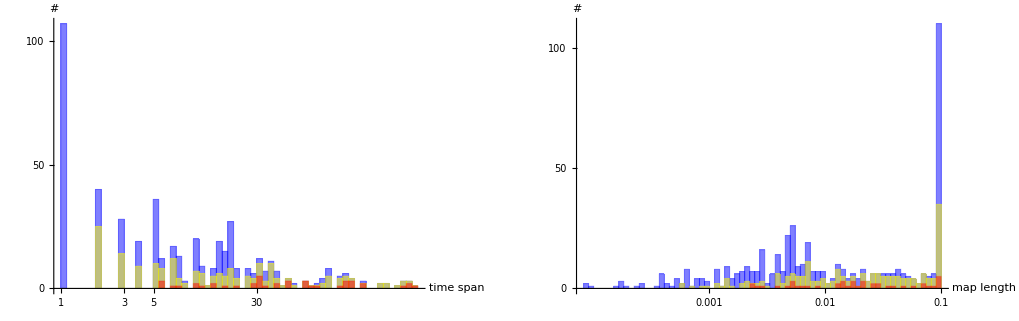

```mathematica
txal50=Select[txal,#[[3]]>sa[[-n50]]&];txal90=Select[txal,#[[3]]>sa[[-n90]]&];
GraphicsRow[{Histogram[{Log[txal[[All,1]]],Log[txal90[[All,1]]],Log[txal50[[All,1]]]},60,ChartStyle->{Blue,Yellow,Red},AxesLabel->{"time\nspan","#"},Ticks->{{{Log[1],"1"},{Log[2],"2"},{Log[3],"3"},{Log[4],"4"},{Log[5],"5"},{Log[10],"10"},{Log[30],"30"},{Log[100],"100"}},{0,50,100}}],Histogram[{Log[txal[[All,2]]],Log[txal90[[All,2]]],Log[txal50[[All,2]]]},60,ChartStyle->{Blue,Yellow,Red},AxesLabel->{"map\nlength","#"},Ticks->{{{Log[0.001],"0.001"},{Log[0.01],"0.01"},{Log[0.1],"0.1"}},{0,50,100}}]}]
```

#### Table of branch properties

Note that all branches are on a single interval

```mathematica
tallyIntervalNumber[blf]
```

{{1,54}}

```mathematica
TableForm[Prepend[blf10,{"Clade","time of origin","map interval"}],TableDepth->2]
```

Clade | time of origin | map interval
{1} | 1 | {{0,0.1}}
{2} | 1 | {{0,0.1}}
{3} | 1 | {{0,0.1}}
{4} | 1 | {{0,0.1}}
{5} | 1 | {{0,0.1}}
{6} | 1 | {{0,0.1}}
{7} | 1 | {{0,0.1}}
{8} | 1 | {{0,0.1}}
{9} | 1 | {{0,0.1}}
{10} | 1 | {{0,0.1}}
{1,9} | 3 | {{0.00269484,0.0216572}}
{3,5} | 4 | {{0.0615051,0.1}}
{3,5} | 12 | {{0.015999,0.0615051}}
{1,4} | 4 | {{0,0.00269484}}
{7,10} | 8 | {{0,0.1}}
{1,4,8} | 8 | {{0,0.00269484}}
{4,8} | 8 | {{0.00269484,0.1}}
{6,9} | 10 | {{0,0.00215397}}
{2,7,10} | 15 | {{0.0140003,0.0253309}}
{2,6} | 15 | {{0.0253309,0.1}}
{1,4,5,8} | 16 | {{0,0.000485901}}
{5,6} | 16 | {{0.00215397,0.015999}}
{3,5,6} | 16 | {{0.015999,0.0253309}}
{3,5,6} | 65 | {{0.0140003,0.015999}}
{2,3,5,6} | 16 | {{0.0253309,0.1}}
{2,3,5,6} | 65 | {{0.00215397,0.0140003}}
{2,4,7,8,10} | 21 | {{0.0189914,0.0253309}}
{4,7,8,10} | 21 | {{0.0253309,0.0712151}}
{2,3,5,6,9} | 28 | {{0.0453142,0.0965451}}
{2,3,5,6,9} | 37 | {{0.0446031,0.0453142}}
{6,7,9,10} | 29 | {{0,0.00215397}}
{7,9,10} | 29 | {{0.00215397,0.00269484}}
{1,7,9,10} | 29 | {{0.00269484,0.0140003}}
{1,7,9,10} | 131 | {{0.0991522,0.1}}
{1,2,7,9,10} | 29 | {{0.0140003,0.0189914}}
{1,2,4,7,8,9,10} | 29 | {{0.0189914,0.0216572}}
{1,2,4,7,8,9,10} | 41 | {{0.0140003,0.0189914}}
{2,4,7,8,9,10} | 29 | {{0.0216572,0.0253309}}
{4,7,8,9,10} | 29 | {{0.0253309,0.0446031}}
{1,7,10} | 34 | {{0.074802,0.1}}
{1,7,10} | 46 | {{0.0712151,0.074802}}
{2,3} | 37 | {{0,0.0140003}}
{1,4,7,8,9,10} | 41 | {{0.00912131,0.0140003}}
{2,3,4,5,6,8,9} | 48 | {{0.0745833,0.0965451}}
{2,3,4,5,6,8} | 48 | {{0.0965451,0.1}}
{1,2,3,4,5,8} | 65 | {{0,0.000485901}}
{2,3,5} | 65 | {{0.000485901,0.00215397}}
{1,3,5,6} | 65 | {{0.0216572,0.0253309}}
{1,2,3,5,6} | 65 | {{0.0253309,0.0446031}}
{1,2,3,5,6,9} | 65 | {{0.0446031,0.0712151}}
{1,2,3,5,6,7,9,10} | 65 | {{0.0712151,0.0745833}}
{1,2,3,5,6,7,9,10} | 133 | {{0.00269484,0.00912131}}
{1,2,3,4,5,6,7,8,10} | 116 | {{0.0965451,0.0991522}}
{2,3,5,6,7,9,10} | 133 | {{0.000485901,0.00269484}}

#### Plotting the SNP on the most substantial branches

These are the SNP on the 9 longest branches (coded by colour):

```mathematica
colsF={Black,Gray,Brown,Red,Orange,Green,Cyan,Magenta,Purple(*,Blue*)};
{big2full,colsF}//TableForm
```

1 | 3 | 4 | 9 | 17 | 25 | 28 | 44 | 50
GrayLevel[0] | GrayLevel[0.5] | RGBColor[0.6, 0.4, 0.2] | RGBColor[1, 0, 0] | RGBColor[1, 0.5, 0] | RGBColor[0, 1, 0] | RGBColor[0, 1, 1] | RGBColor[1, 0, 1] | RGBColor[0.5, 0, 0.5]

In this diagram, genome #1 is the bottom row, #10 the top. Thus, branch 1 leads down to to 1 (black), branch 14 leads down to {7, 10} (grey), and so on.  These sets can be seen in the genealogies above.

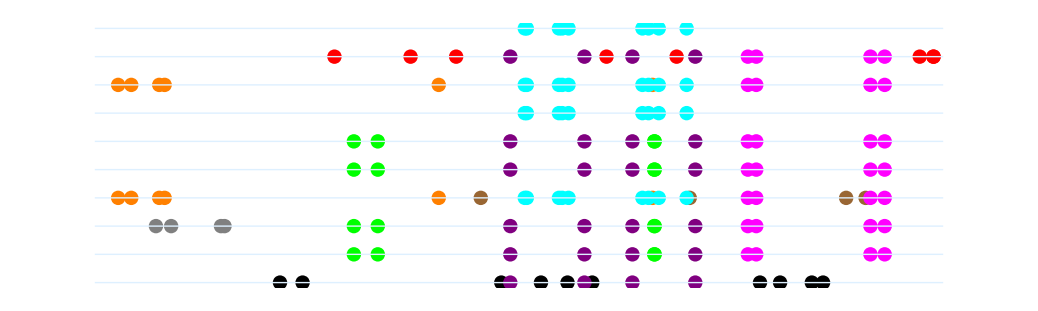

```mathematica
ggBig=Graphics[Join[{PointSize[0.01]},Join@@MapThread[{#2,plotSNP[#1,pop10full]}&,{big2full,colsF}],{LightBlue},plotGenomes[10,0.1]],AspectRatio->0.3]
```

This uses the colour code above.   The blocks are shown in two different orders, to make clear that they often obscure each other:

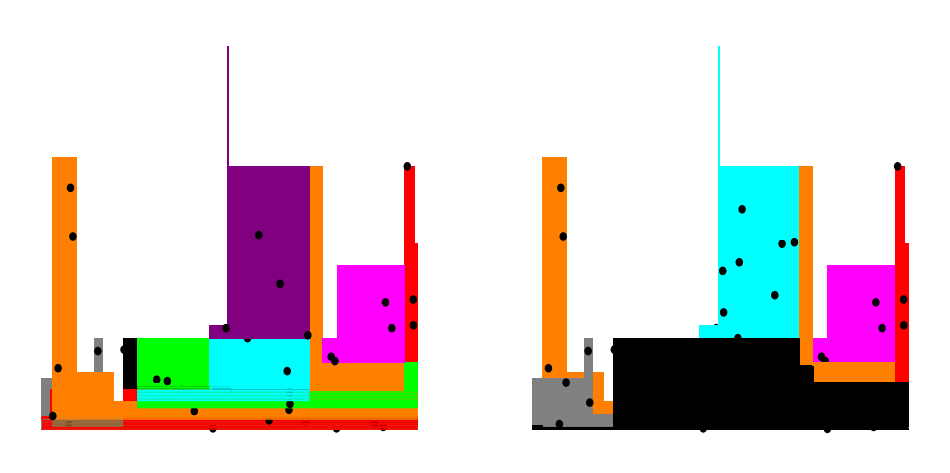

```mathematica
gr=MapThread[Show[plotBranchFull[blf10⟦#1⟧,#2,pl10,0.1],Graphics[Prepend[Table[Disk[snp10full⟦#,j,{2,1}⟧,{0.001,3}],{j,Length[snp10full⟦#⟧]}],Black]],PlotRange->{{0,0.1},{0,270}},AspectRatio->1]&,{big2full,colsF}];
GraphicsRow[{Show[gr],Show[Reverse[gr]]}]
```

These blocks may be overlaid.  This animation shows them separately, along with SNP superimposed:

```mathematica
ListAnimate[MapThread[Show[plotBranchFull[blf10⟦#1⟧,#2,pl10,0.1],Graphics[Prepend[Table[Disk[snp10full⟦#,j,{2,1}⟧,{0.001,3}],{j,Length[snp10full⟦#⟧]}],White]],PlotRange->{{0,0.1},{0,270}},AspectRatio->1]&,{big2full,colsF}]]
```

This shows all the 54 blocks:

```mathematica
cf=ColorData["DarkRainbow"];gg[k_]:=Show[plotBranchFull[blf10⟦k⟧,cf[(k-1)/54],pl10,0.1],Graphics[Prepend[Table[Disk[snp10full⟦k,j,{2,1}⟧,{0.001,3}],{j,Length[snp10full⟦k⟧]}],Black]],PlotRange->{{0,0.1},{0,270}},AspectRatio->1,PlotLabel->"branch "~~ToString[k]];
ListAnimate[Table[gg[k],{k,1,54}]]
```

These are the data used in the block diagrams in the paper. The two versions only differ in the order with which blocks are overlaid.

-Graphics-

## Selective sweep

### Example with s=0.1, 2N=400, R=0.2, 20 genomes

#### Setting up the sweep

There is substantial variation between replicate sweeps, which arises mainly from random variation in the time at which exponential growth is established.  The probability of fixation is ~2s, and conditional on fixation, the sweep is established as if starting at an initial frequency p_0that is exponentially distributed, with mean 1/(2s). This particular sweep has a rather long delay. The trajectory itself is spliced onto a very long run of 1’s, so that the simulation can continue back until all lineages have coalesced.

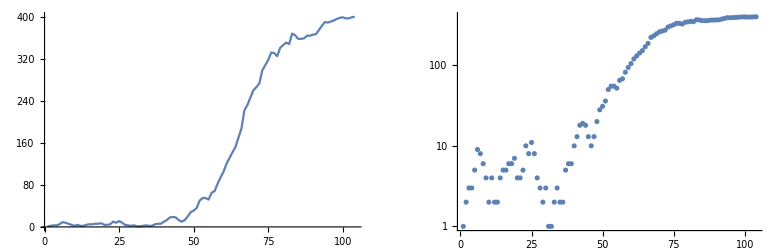

{104}

```mathematica
mrx=makeRepsFix[0.1,400,1,1];
selB=Join[ConstantArray[1,10^6],mrx[[1]]];
GraphicsRow[{Show[ListLinePlot[mrx[[1]]],PlotRange->All],Show[ListLogPlot[mrx[[1]]],PlotRange->All]}]
Length/@mrx
```

#### Setting up ancestries and genealogies, and throwing down SNP: μ/r=2

We use the same sweep as above, as coded in selB; it takes 104 generations to fixation.

This iterates 20 lineages back through time, to the beginning of the sweep. R=0.1, 2N=400; 2NR=40.  Complete coalescence takes 4272 generations in total.

```mathematica
Timing[time=0;sweepB20=makeC[20,0.2,400,selB];
Length[sweepB20]]
```

{39.6301,4272}

This sets the ancestral genotype, prior to the mutation, to zero:

```mathematica
tMut=bounds[Reverse[selB]][[-1,1]];
sweepB20=Join[sweepB20[[1;;tMut-1]],Replace[sweepB20[[tMut;;-1]],{1,x__}:>{0,x},{2}]];
```

This sets up a list of genealogies for each of the 428 intervals along the 20cM stretch of genome. We track yy, the interval it is working on. This is quite slow (and an inefficient algorithm, since it works independently on each genealogy).

```mathematica
ints20=intervals[sweepB20,0.2];
Timing[genB20=(yy=#;makeGenealogyFull[sweepB20,yy,0.2])&/@ints20;]
```

{6394.2,Null}

This generates a set of genealogies that have an outgroup added, and also that specify the associated genotype at the selected locus. It takes some time to add the ancestries:

```mathematica
genB20New=Table[addOutgroup[addGenotype[genB20[[j]],sweepB20,20,ints20[[j]],0.2],{10^5,{},0}],{j,Length[ints20]}];
```

This  throws 937 SNP onto the 730 branches and 20 genomes (using addSNPFull). There are 4762 segregating alleles:

```mathematica
blB20=branchListFull[sweepB20,0.2];
snpB20=makeSNP[posBlockFull[sweepB20,#,0.2],2]&/@blB20;
popB20=addSNP[blB20,snpB20];
```

```mathematica
{Length[snpB20],Total[Length/@snpB20],Dimensions[popB20],Total[Length/@popB20]}
```

{730,937,{20},4762}

This saves the example. Note that there are two sets of genealogies: genB20 which includes only the sampled 20 genomes, and genB20New which includes the selected background and an outgroup. blB20 lists branches only from the first set.

```mathematica
Save["Big sweeps s=0.1, 2N=400 R=0.2 20 genomes 2 Jan",{selB,sweepB20,genB20,genB20New,blB20,snpB20,popB20,ints20}];
```

```mathematica
<<"Big sweeps s=0.1, 2N=400 R=0.2 20 genomes 2 Jan";
```

#### Description of the genealogies

This shows depth (top right) and mean pairwise divergence (lower left) for the genealogies.  The lower right plot shows SNP patterns, comparing the # of segregating sites (black) with π (blue) along the genome. The classic theory works on average, but not necessarily in any one instance, even for a rather clear sweep..

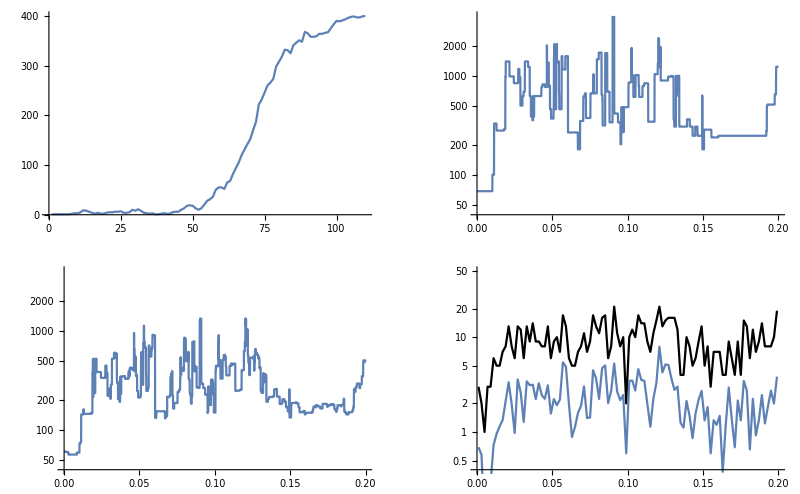

```mathematica
dgf=genFunction[DepthOfGenealogy,x,genB20,intervals[sweepB20,0.2]];
pwf=genFunction[MeanPairwiseDivergence,x,genB20,intervals[sweepB20,0.2]];
GraphicsGrid[{{ListLinePlot[Take[selB,-110]],LogPlot[dgf,{x,0,0.2},PlotRange->{{0,0.2},{40,4000}}]},
{LogPlot[pwf,{x,0,0.2},PlotRange->{{0,0.2},{40,4000}}],Show[ListLogPlot[Transpose[{Range[δ/2,0.2-δ/2,δ],nSites/@snpW}],PlotStyle->Black,Joined->True,PlotRange->{{0,0.2},{0.4,50}}],
ListLogPlot[Transpose[{Range[δ/2,0.2-δ/2,δ],piSNP/@snpW}],Joined->True]]}}]
```

The left plot is a histogram of the block areas, on a log_10 scale - centred on about 0.1; the right two plots give the distribution of # SNP (log and normal scale). Most branches have no SNP; 604/937 SNP are on 51 branches with at least 5,  438 are on the 25 branches with at least 10, and 209 are on the 8 branches with at least 20.

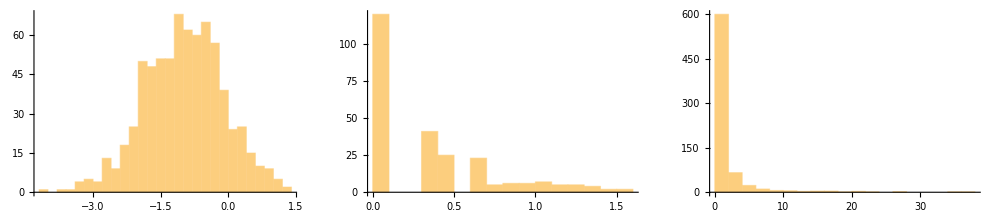

```mathematica
GraphicsRow[{Histogram[Log[10,branchAreaFull[sweepB20,0.2]]],Histogram[Log[10,Length/@snpB20],20],Histogram[Length/@snpB20,20]}]
```

#### Genealogies along the genome

This shows how the genealogy  along the genome, on a log scale.  The genomic interval is shown below each plot, and the numbers label the branches.  Red indicates branches that originate on the new (fitter) genetic background.

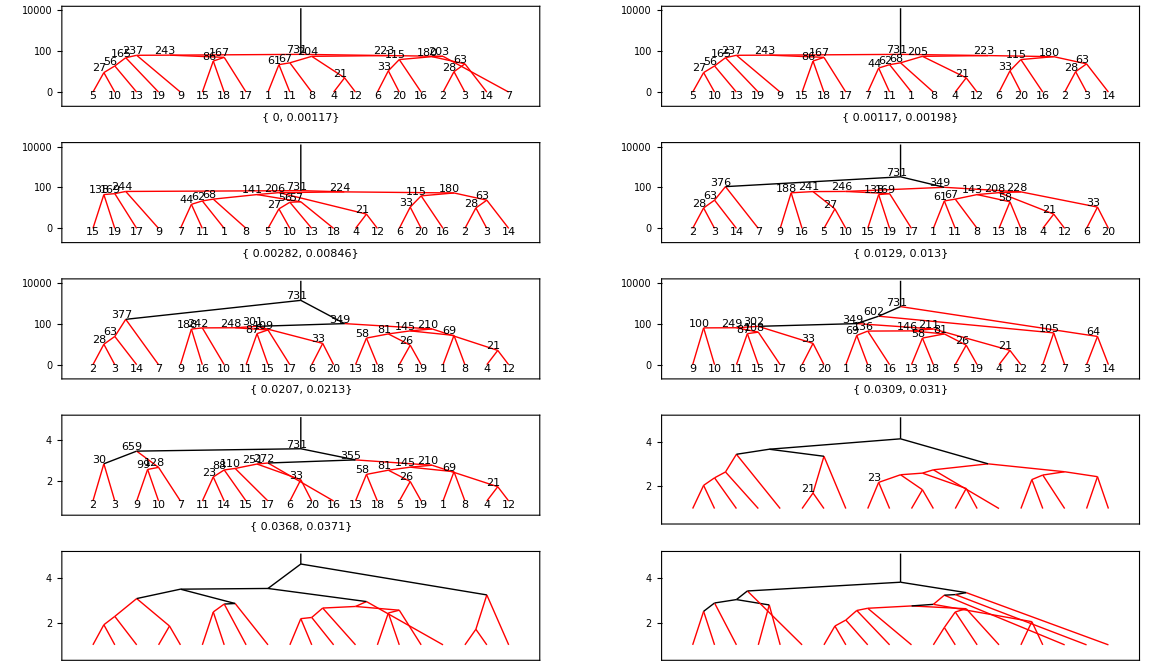

```mathematica
tks={1.+Log[10,1+#],ToString[#]}&/@{0,10,100,1000,10000};
hh[j_]:=Module[{mg},
mg=MakeGenealogyPlot[genB20New[[j,3,2]]];xy=plotLogCoords[1,1][0,mg[[2]]];
Show[PlotGenealogy[mg,MakeGenealogyPlot->False,NodeFunction->plotLogCoords[1,1],BranchStyle->plotBranchStyle[{Black},{Red}]],
Graphics[{Black,Line[{xy,{xy[[1]],5.1}}]}],
PlotRange->{{-1,20},{0.4,5.1}},Frame->True,FrameLabel->ToString[PaddedForm[ints20[[j]],3]],FrameTicks->{{tks,None},{None,None}}]];
ii={1,2,5,10,25,40,60,100,200,420};
GraphicsGrid[Partition[hh/@ii,2]]
```

Below, doing the same, colouring in the branches properly (by showing where the recombination onto a different background happens), and marking times when p=1/400, 0.1, 0.5, 0.9 (at {22,38,53,110 generations; dashed lines}). Note that coalescence can only occur within the same background (i.e. black with black or red with red). In the recent past, recombinations may occur within the derived (red) background; further back, when the fitter allele is still rare, recombination will almost certainly be onto the ancestral background (red→black), rather than in the opposite direction. Recombination out is likely when p is below 0.5, and must happen before the origin of the mutation if coalescence is to be avoided. Up to map position ~0.01, there is some rearrangement amongst recent genealogies, but all lineages coalesce in a MRCA associated with the new mutation (marked 731 in the top left and top middle panels).  The first recombination splits the genealogy into clades of size {4,16}; the number of deep branches (that trace back >110 generations, deeper than the top dotted line) for the 9 trees shown below is {1,1,2,2,3,3,5,6,6}.  Note that under the standard coalescent, the expected time for a large sammple to coalesce down to  6 lineages is 120 generations - so we expect that large samples will already be substantially thinned before the sweep is reached.  By map position 0.0129 (top right), we have had 5 recombinations out  (and one back) at {{38,45},47,65,90}.  At the end of the genome (map position 0.2; bottom right) there have been about 7 recombination events. One can accurately calculate the expectations for these numbers using the standard coalescent.

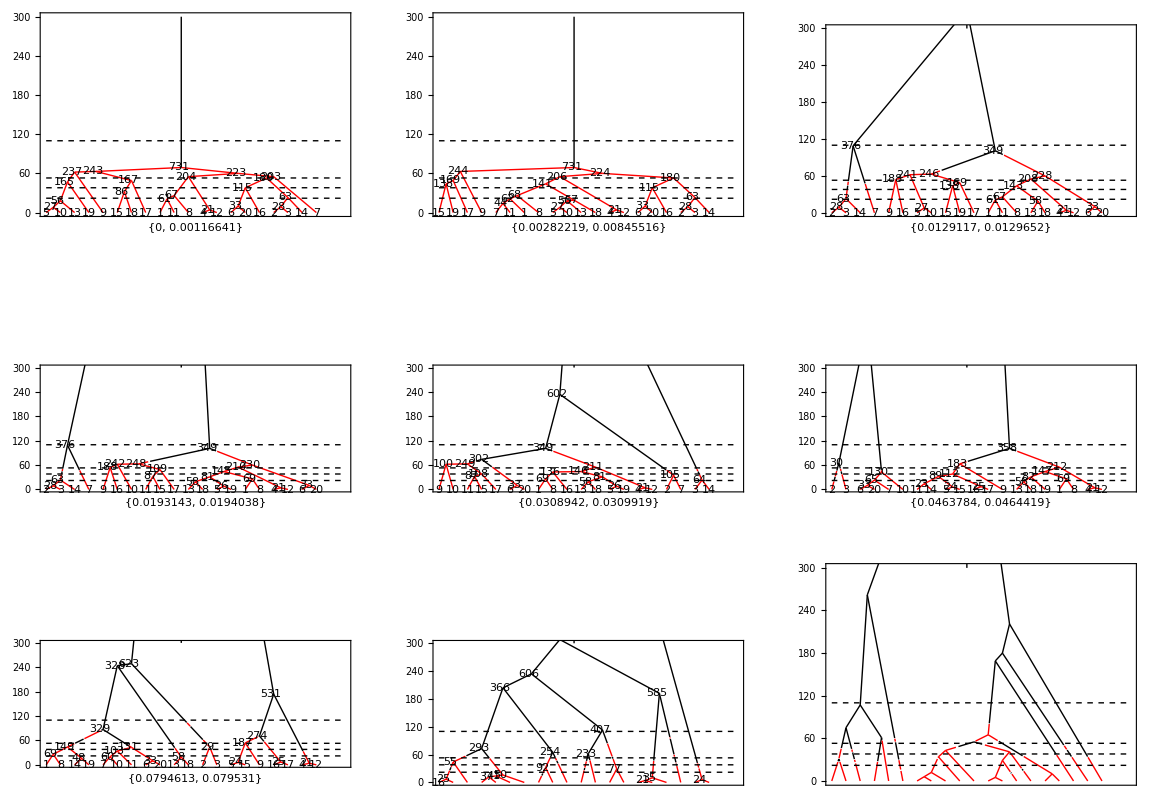

{{0,0.00116641},{0.00282219,0.00845516},{0.0129117,0.0129652},{0.0193143,0.0194038},{0.0308942,0.0309919},{0.0463784,0.0464419},{0.0794613,0.079531},{0.133436,0.133529},{0.197523,0.198033}}

```mathematica
mx=300;
hh[j_]:=Module[{mg},
mg=MakeGenealogyPlot[genB20New[[j,3,2]]];xy=plotCoords[1][0,mg[[2]]];
Show[PlotGenealogy[mg,MakeGenealogyPlot->False,NodeFunction->plotCoords[1],
BranchGraphic->mosaicBranch[mg,sweepB20,ints20[[j]],0.2,{{Black},{Red}}]],
Graphics[{Black,Line[{xy,{xy[[1]],mx}}]}],(* vertical branch back from the root *)
Graphics[Join[{Black,Dashing[{0.01,0.01}]},Line[{{0,#},{21,#}}]&/@{110,53,38,22}]],
FrameLabel->ToString[ints20[[j]]],Frame->True,FrameTicks->{None,Automatic},PlotRange->{{0,21},{0,mx}},AspectRatio->0.7]];
ii={1,5,10,20,40,80,160,320,420};
GraphicsGrid[Partition[hh/@ii,3]]
ints20[[ii]]
```

#### General considerations

The following sections try various ways of identifying sets of “interesting” branches.

A first step in identifying a selective sweeps is to find branches that are associated with that sweep.  The simplest case is where a single mutation sweeps through an extremely large population, which is sampled immediately after the sweep.  Then, lineages either coalesce soon after the mutation arises, when it is still in small numbers, or they recombine out and coalesce much further back.  However, a large sample will coalesce down to  k lineages in 2N_e/k generations, where N_e is the haploid effective population size.  Thus,  there can be appreciable coalescence more recently than the sweep, which would happen even in its absence. This is seen in the example here, where N_e is only 400;  at the focal locus we have only 10 lineages out of the original 20, at the time when the sweeping allele is at 50%.

#### Branches that are associated with the selected locus

Identifying branches with coalescences that occurred at or more recently than the sweep seems problematic.  Here, we find 18 branches that cover the selected locus; 8 of these are not nested within others. The table shows the genomic interval; the time of the coalescence; and the set of descendant branches.  Note that this list includes sets of descendants that are nested within other sets for some of the genome; however, we list them separately, because they are not nested over their whole extent. For example, at the selected locus, {5,10} coalesce first, at generation 8, and then, at generation 18 back from the present, {5,10,13} coalesce.  However, the branch {5,10} extends out to 1.68cM, whereas {5.10.13} extends back only out to 0.846cM.  Thus, {5,10} is only nested within {5,10,13} over part of its extent.

```mathematica
blB20sel=DeleteCases[Cases[blB20,{_,_,{{0,_},___}}],{{_},_,_}];
blB20notNested=Select[blB20sel,Not[nestedQ[#,blB20sel]]&];
TableForm[Sort[Reverse/@blB20notNested],TableDepth->2]
Length/@{blB20sel,blB20notNested}
```

{{0,0.00282219}} | 60 | {1,2,3,4,6,7,8,11,12,14,16,20}
{{0,0.00282219}} | 63 | {5,9,10,13,15,17,18,19}
{{0,0.00845516}} | 18 | {5,10,13}
{{0,0.0107685}} | 53 | {2,3,6,14,16,20}
{{0,0.0168376}} | 8 | {5,10}
{{0,0.0278147}} | 23 | {2,3,14}
{{0,0.0905804}} | 10 | {6,20}
{{0,0.163959}} | 4 | {4,12}

{18,8}

For the 8 branches, these are the # of descendants; times of origin; extent; # SNP; and areas. Only three carry more than 1 SNP, and those three make up all but 3% of the area. However, only the last three branches are actually generated by the sweep - that is, coalesce within the favourable background whilst it is still rare:

```mathematica
xx=Flatten[Position[blB20,#]&/@blB20notNested];
TableForm[{Length/@blB20notNested[[All,1]],blB20notNested[[All,2]],blB20notNested[[All,3]],Length/@snpB20⟦xx⟧,branchAreaFull[sweepB20,0.2][[xx]]},TableDepth->2]
```

2 | 2 | 2 | 3 | 3 | 6 | 12 | 8
4 | 8 | 10 | 18 | 23 | 53 | 60 | 63
{{0,0.163959}} | {{0,0.0168376}} | {{0,0.0905804}} | {{0,0.00845516}} | {{0,0.0278147}} | {{0,0.0107685}} | {{0,0.00282219}} | {{0,0.00282219}}
35 | 1 | 10 | 1 | 4 | 0 | 0 | 1
18.6594 | 0.537201 | 2.88222 | 0.0638996 | 2.52994 | 0.0695472 | 0.0253997 | 0.0169331

This shows the 8 non-nested branches that are associated with the focal genealogy. Only four blocks are really visible.   The light pink area at left is where the whole genealogy coalesces in the sweep

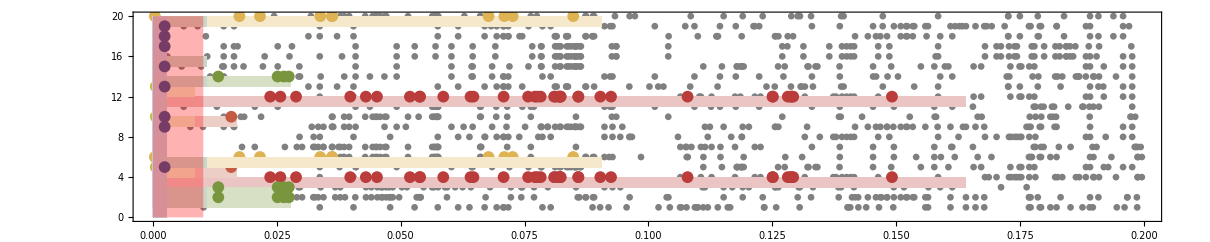

```mathematica
ppb=Flatten[Position[blB20,#]&/@blB20notNested];
cf=ColorData["DarkRainbow"];cols=cf/@Range[1,0,-1/(Length[ppb]-1)];nb=Length[snpB2];
gb[b_,c_]:=Show[plotBlockFull[blB20[[b]],Lighter[c,0.7],sweepB20,0.2],Graphics[{c,PointSize[0.007],plotSNP[b,popB20]}],PlotRange->{{0,0.21},{0,21}}];
cr=coalescedRegions[sweepB20[[70]],20];
Show[Graphics[plotSNP[Complement[Range[nb],ppb],ConstantArray[Gray,nb],0.004,popB20]],
MapThread[gb,{ppb,cols}],
Graphics[Join[{Opacity[0.3,Red]},Rectangle[{#[[1]],0},{#[[2]],20}]&/@cr]],AspectRatio->0.2,Frame->True]
```

#### Showing the largest branches: 30 non-tip branches, area>2

These are the # of blocks and their areas, for  different threshold areas. 7 of the branches give 22% of the area, whilst 22 give 44%. I choose a threshold area of 2, and restrict to non-tips which gives 33% of the area.

```mathematica
ba=branchAreaFull[sweepB20,0.2];
ss[th_]:=(bas=Select[ba,#≥th&];{th,Length[bas],Total[bas],Total[bas]/Total[ba]});
TableForm[ss/@{0.5,1,2,5,10,15}]
```

0.5 | 149 | 381.959 | 0.847243
1 | 90 | 340.934 | 0.756243
2 | 49 | 281.021 | 0.623347
5 | 22 | 199.645 | 0.442843
10 | 7 | 98.4184 | 0.218307
15 | 2 | 36.7701 | 0.0815617

```mathematica
big=Select[Range[Length[blB20]],(ba[[#]]>=2)∧(blB20[[#,2]]>1)&];
{Length[big],Total[ba[[big]]]/Total[ba],Total[Length/@snpB20[[big]]]/Total[Length/@snpB20]//N}
```

{32,0.329255,0.308431}

Identifying branches with coalescences at or more recently than the sweep seems problematic.  Here, I find 32 non-tip branches that cover 33% of the area and 31% of SNP; two of these are  nested, and so dropped, leaving 30 branches.

```mathematica
blB20notNested=Select[blB20[[big]],Not[nestedQ[#,blB20[[big]]]]&];
TableForm[Sort[Reverse/@blB20notNested],TableDepth->2]
Length/@{blB20[[big]],blB20notNested}
```

{{0,0.0278147}} | 23 | {2,3,14}
{{0,0.0905804}} | 10 | {6,20}
{{0,0.163959}} | 4 | {4,12}
{{0.00845516,0.0826403}} | 19 | {13,18}
{{0.0129117,0.0203284}} | 109 | {2,3,7,14}
{{0.0129117,0.0330864}} | 101 | {1,4,5,6,8,9,10,11,12,13,15,16,17,18,19,20}
{{0.0207029,0.0306668}} | 164 | {2,3,7,14}
{{0.0352883,0.049621}} | 65 | {2,3}
{{0.0377105,0.0699155}} | 44 | {1,8,13,18,19}
{{0.0377105,0.2}} | 6 | {5,15}
{{0.040501,0.0509682}} | 101 | {1,4,5,8,9,11,12,13,14,15,16,17,18,19}
{{0.040501,0.0555959}} | 43 | {6,7,10,20}
{{0.0422193,0.185441}} | 7 | {16,17}
{{0.0555959,0.0867949}} | 43 | {6,7,10,11,20}
{{0.0684998,0.0836397}} | 44 | {2,3}
{{0.0720953,0.0862156}} | 71 | {5,9,15,16,17}
{{0.080859,0.0823478}} | 316 | {1,2,3,5,6,7,8,9,10,11,13,14,15,16,17,18,19,20}
{{0.0899643,0.0922881}} | 340 | {2,3,5,6,7,8,9,10,11,13,14,15,16,17,18,19,20}
{{0.0935484,0.122784}} | 43 | {4,7,12}
{{0.100693,0.105872}} | 150 | {2,3,4,5,6,7,8,9,11,12,14,15,19,20}
{{0.1016,0.105872}} | 174 | {1,10,13,16,17,18}
{{0.10589,0.122784}} | 73 | {10,11,14,16,17,19}
{{0.106769,0.111089}} | 175 | {2,3,4,5,6,7,8,9,12,13,15,18,20}
{{0.117552,0.126048}} | 144 | {1,2,3,9,18,20}
{{0.122784,0.133868}} | 73 | {7,10,11,14,16,17,19}
{{0.126275,0.13198}} | 86 | {1,5,15}
{{0.130813,0.163959}} | 10 | {4,8,12}
{{0.138979,0.163959}} | 32 | {4,8,12,16,17}
{{0.180743,0.195878}} | 14 | {4,14}
{{0.00116641,0.0129117},{0.158675,0.180407}} | 14 | {7,11}
{{0.0579233,0.0602473},{0.0610882,0.0672732}} | 109 | {5,6,7,9,10,11,14,15,16,17,20}
{{0.0823478,0.0840355},{0.0868214,0.0894669},{0.0899643,0.0922881}} | 174 | {1,4,12}

{32,32}

For the 30 branches, these are the # of descendants; times of origin; extent; # SNP; and areas. One branch(#347) is disjunct.  Not many are generated by the sweep, or associated with it, in the sense that only 3 begin at zero, and only  9 originate between 40 and 80 generations back (which is when the sweep is inducing most coalescence)

```mathematica
ppb=Flatten[Position[blB20,#]&/@blB20notNested];cols=ColorData["DarkRainbow"]/@Range[1,0,-1/(Length[ppb]-1)];
TableForm[Prepend[Transpose[{ppb,cols,Length/@blB20notNested[[All,1]],blB20notNested[[All,2]],Length/@snpB20⟦ppb⟧,branchAreaFull[sweepB20,0.2][[ppb]],blB20notNested[[All,3]]}],{"index","colour","# desc","t","# SNP","area","{r_0,r_1}"}],TableDepth->2]
```

index | colour | # desc | t | # SNP | area | {r_0,r_1}
21 | RGBColor[0.72987, 0.239399, 0.230961] | 2 | 4 | 35 | 18.6594 | {{0,0.163959}}
24 | RGBColor[0.72987, 0.239399, 0.230961] | 2 | 6 | 20 | 11.7729 | {{0.0377105,0.2}}
25 | RGBColor[0.72987, 0.239399, 0.230961] | 2 | 7 | 17 | 6.41979 | {{0.0422193,0.185441}}
29 | RGBColor[0.72987, 0.239399, 0.230961] | 2 | 44 | 3 | 3.85298 | {{0.0684998,0.0836397}}
30 | RGBColor[0.7539484838709677, 0.3204846451612904, 0.2520088064516129] | 2 | 65 | 10 | 5.08574 | {{0.0352883,0.049621}}
33 | RGBColor[0.7807023548387096, 0.4105798064516129, 0.2753952580645161] | 2 | 10 | 10 | 2.88222 | {{0,0.0905804}}
35 | RGBColor[0.8074562258064516, 0.5006749677419354, 0.29878170967741935] | 3 | 10 | 3 | 2.10807 | {{0.130813,0.163959}}
40 | RGBColor[0.8295987419354838, 0.5734942580645161, 0.3095072580645161] | 2 | 14 | 10 | 2.81302 | {{0.180743,0.195878}}
44 | RGBColor[0.8505884193548386, 0.6419945806451612, 0.3170675806451613] | 2 | 14 | 5 | 2.73779 | {{0.00116641,0.0129117},{0.158675,0.180407}}
58 | RGBColor[0.8715780967741935, 0.7104949032258064, 0.3246279032258065] | 2 | 19 | 5 | 2.81091 | {{0.00845516,0.0826403}}
63 | RGBColor[0.8632332580645161, 0.739004, 0.3216035483870968] | 3 | 23 | 4 | 2.52994 | {{0,0.0278147}}
93 | RGBColor[0.8423164838709677, 0.750374, 0.31404290322580647] | 5 | 32 | 7 | 2.72372 | {{0.138979,0.163959}}
130 | RGBColor[0.8213997096774194, 0.761744, 0.3064822580645161] | 4 | 43 | 8 | 6.99008 | {{0.040501,0.0555959}}
131 | RGBColor[0.7766135806451613, 0.7482939354838709, 0.2958782580645161] | 5 | 43 | 10 | 4.0976 | {{0.0555959,0.0867949}}
132 | RGBColor[0.7159145483870968, 0.7182971612903225, 0.28324535483870966] | 3 | 43 | 7 | 2.39647 | {{0.0935484,0.122784}}
147 | RGBColor[0.6552155161290323, 0.6883003870967741, 0.2706124516129032] | 5 | 44 | 4 | 2.0393 | {{0.0377105,0.0699155}}
274 | RGBColor[0.5912414838709678, 0.6542766774193548, 0.2606708387096774] | 5 | 71 | 13 | 3.86921 | {{0.0720953,0.0862156}}
292 | RGBColor[0.5239924516129032, 0.6162260322580645, 0.25342051612903227] | 6 | 73 | 7 | 4.93033 | {{0.10589,0.122784}}
293 | RGBColor[0.4567434193548387, 0.5781753870967742, 0.2461701935483871] | 7 | 73 | 2 | 2.33088 | {{0.122784,0.133868}}
326 | RGBColor[0.4002746451612903, 0.5452579032258065, 0.24563819354838712] | 3 | 86 | 5 | 2.28132 | {{0.126275,0.13198}}
347 | RGBColor[0.3599762580645161, 0.5200401612903226, 0.2551836774193548] | 3 | 174 | 8 | 5.69969 | {{0.0823478,0.0840355},{0.0868214,0.0894669},{0.0899643,0.0922881}}
349 | RGBColor[0.3196778709677419, 0.49482241935483867, 0.2647291612903226] | 16 | 101 | 23 | 13.2438 | {{0.0129117,0.0330864}}
358 | RGBColor[0.2888518387096774, 0.471930064516129, 0.28239380645161294] | 14 | 101 | 12 | 5.05503 | {{0.040501,0.0509682}}
376 | RGBColor[0.2801279677419355, 0.4544636129032258, 0.3190031612903226] | 4 | 109 | 4 | 2.88023 | {{0.0129117,0.0203284}}
377 | RGBColor[0.2714040967741936, 0.43699716129032257, 0.3556125161290323] | 4 | 164 | 12 | 7.41051 | {{0.0207029,0.0306668}}
379 | RGBColor[0.2637299032258065, 0.41798329032258064, 0.39607748387096775] | 11 | 109 | 5 | 3.09476 | {{0.0579233,0.0602473},{0.0610882,0.0672732}}
465 | RGBColor[0.26025441935483873, 0.3927797419354839, 0.45196490322580646] | 6 | 144 | 7 | 2.56487 | {{0.117552,0.126048}}
492 | RGBColor[0.256778935483871, 0.3675761935483871, 0.5078523225806452] | 14 | 150 | 8 | 3.78986 | {{0.100693,0.105872}}
534 | RGBColor[0.25313761290322584, 0.34474209677419354, 0.5586981612903226] | 6 | 174 | 8 | 3.04678 | {{0.1016,0.105872}}
544 | RGBColor[0.24800374193548388, 0.343233064516129, 0.5641697741935483] | 13 | 175 | 5 | 2.09885 | {{0.106769,0.111089}}
680 | RGBColor[0.24286987096774193, 0.3417240322580645, 0.5696413870967741] | 18 | 316 | 2 | 2.07546 | {{0.080859,0.0823478}}
694 | RGBColor[0.237736, 0.340215, 0.575113] | 17 | 340 | 10 | 4.14525 | {{0.0899643,0.0922881}}

This shows the 30 non-nested, non-tip branches that are associated with the focal genealogy. The light pink rectangle at left is where the whole genealogy coalesces in the sweep.  The substantial branches seem to be concentrated near the sweep, even though SNP diversity is high all along the genome, except for the leftmost 1cM

```mathematica
ppb=Flatten[Position[blB20,#]&/@blB20notNested];
cf=ColorData["DarkRainbow"];cols=cf/@Range[1,0,-1/(Length[ppb]-1)];nb=Length[snpB2];
gb[b_,c_]:=Show[plotBlockFull[blB20[[b]],Lighter[c,0.7],sweepB20,0.2],Graphics[{c,PointSize[0.005],plotSNP[b,popB20]}],PlotRange->{{0,0.21},{0,21}}];
cr=coalescedRegions[sweepB20[[70]],20];
Show[Graphics[plotSNP[Complement[Range[nb],ppb],ConstantArray[Gray,nb],0.003,popB20]],
MapThread[gb,{ppb,cols}],
Graphics[Join[{Opacity[0.3,Red]},Rectangle[{#[[1]],0},{#[[2]],20}]&/@cr]],AspectRatio->0.2,Frame->True]
```

-Graphics-

This shows genealogies at 0, 0.01, 0.02, 0.05, 0.20, on two different vertical scales. The first “escape” is just beyond 1cM, but the genealogy still retains the effects of the sweep out to 5cM or so:

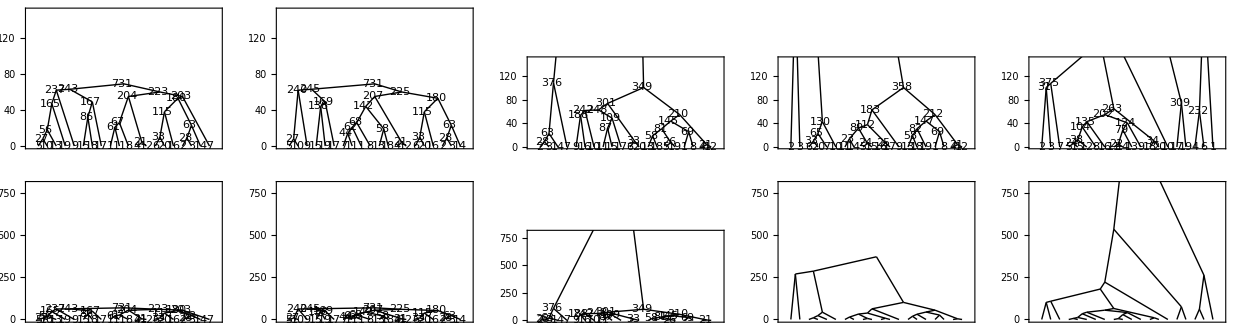

{{0,0.00116641},{0.00845516,0.0101709},{0.0199083,0.0203284},{0.049621,0.0504018},{0.199885,0.2}}

```mathematica
hh[j_,ym_]:=Show[PlotGenealogy[genB20[[j]],NodeFunction->plotCoords[1]],PlotRange->{{-1,20},{0,ym}},Frame->True,FrameTicks->{None,Automatic},AspectRatio->0.7];
ii={1,6,22,87,-1};
GraphicsGrid[{hh[#,150]&/@ii,hh[#,800]&/@ii}]
ints20[[ii]]
```

These are the 30 branches; the vertical scale is truncated at 800:

```mathematica
gr=MapThread[Show[plotBranchFull[blB20⟦#1⟧,#2,sweepB20,0.2],Graphics[Prepend[Table[Disk[snpB20⟦#,j,{2,1}⟧,{0.001,3}],{j,Length[snpB20⟦#⟧]}],Black]],PlotRange->{{0,0.2},{0,800}},AspectRatio->1]&,{ppb,cols}];
GraphicsRow[{Show[gr],Show[Reverse[gr]]}]
```

-Graphics-

This shows all 30 of the “substantial” blocks

```mathematica
cf=ColorData["DarkRainbow"];gg[k_]:=Show[plotBranchFull[blB20⟦ppb[[k]]⟧,cf[(k-1)/Length[ppb]],sweepB20,0.2],Graphics[Prepend[Table[Disk[snpB20⟦ppb[[k]],j,{2,1}⟧,{0.001,3}],{j,Length[snpB20⟦ppb[[k]]⟧]}],Black]],PlotRange->{{0,0.2},{0,800}},AspectRatio->1,PlotLabel->"branch "~~ToString[ppb[[k]]]];
ListAnimate[Table[gg[k],{k,1,Length[ppb]}]]
```

#### Showing the largest branches: 49 branches, area>2

With a threshold area of 2, including tip branches, we include 62% of the area and 61% of SNP:

```mathematica
ba=branchAreaFull[sweepB20,0.2];
big=Select[Range[Length[blB20]],(ba[[#]]>=2)&];
{Length[big],Total[ba[[big]]]/Total[ba],Total[Length/@snpB20[[big]]]/Total[Length/@snpB20]//N}
```

{49,0.623347,0.614728}

None of these are nested. This sorts by left edge of the branch, and gives the extent, the time of origin,  the descendants, and the area:

```mathematica
blB20notNested=Select[blB20[[big]],Not[nestedQ[#,blB20[[big]]]]&];
tt=Sort[Reverse/@blB20notNested];
TableForm[Transpose[{tt[[All,1]],tt[[All,2]],tt[[All,3]],ba[[big]]}],TableDepth->2]
Length/@{blB20[[big]],blB20notNested}
```

{{0,0.0278147}} | 23 | {2,3,14} | 18.1107
{{0,0.0905804}} | 10 | {6,20} | 10.734
{{0,0.163959}} | 4 | {4,12} | 14.7598
{{0,0.2}} | 1 | {1} | 7.57225
{{0,0.2}} | 1 | {2} | 8.80658
{{0,0.2}} | 1 | {3} | 7.79242
{{0,0.2}} | 1 | {6} | 8.53991
{{0,0.2}} | 1 | {7} | 11.1378
{{0,0.2}} | 1 | {8} | 6.59035
{{0,0.2}} | 1 | {9} | 8.79924
{{0,0.2}} | 1 | {10} | 5.38478
{{0,0.2}} | 1 | {11} | 2.16372
{{0,0.2}} | 1 | {13} | 3.74816
{{0,0.2}} | 1 | {14} | 4.05649
{{0,0.2}} | 1 | {15} | 5.86948
{{0,0.2}} | 1 | {16} | 5.21093
{{0,0.2}} | 1 | {17} | 3.30748
{{0,0.2}} | 1 | {18} | 18.6594
{{0,0.2}} | 1 | {19} | 11.7729
{{0,0.2}} | 1 | {20} | 6.41979
{{0.00845516,0.0826403}} | 19 | {13,18} | 3.85298
{{0.0129117,0.0203284}} | 109 | {2,3,7,14} | 5.08574
{{0.0129117,0.0330864}} | 101 | {1,4,5,6,8,9,10,11,12,13,15,16,17,18,19,20} | 2.88222
{{0.0207029,0.0306668}} | 164 | {2,3,7,14} | 2.10807
{{0.0352883,0.049621}} | 65 | {2,3} | 2.81302
{{0.0377105,0.0699155}} | 44 | {1,8,13,18,19} | 2.73779
{{0.0377105,0.2}} | 6 | {5,15} | 2.81091
{{0.040501,0.0509682}} | 101 | {1,4,5,8,9,11,12,13,14,15,16,17,18,19} | 2.52994
{{0.040501,0.0555959}} | 43 | {6,7,10,20} | 2.72372
{{0.0422193,0.185441}} | 7 | {16,17} | 6.99008
{{0.0555959,0.0867949}} | 43 | {6,7,10,11,20} | 4.0976
{{0.0684998,0.0836397}} | 44 | {2,3} | 2.39647
{{0.0720953,0.0862156}} | 71 | {5,9,15,16,17} | 2.0393
{{0.080859,0.0823478}} | 316 | {1,2,3,5,6,7,8,9,10,11,13,14,15,16,17,18,19,20} | 3.86921
{{0.0899643,0.0922881}} | 340 | {2,3,5,6,7,8,9,10,11,13,14,15,16,17,18,19,20} | 4.93033
{{0.0935484,0.122784}} | 43 | {4,7,12} | 2.33088
{{0.100693,0.105872}} | 150 | {2,3,4,5,6,7,8,9,11,12,14,15,19,20} | 2.28132
{{0.1016,0.105872}} | 174 | {1,10,13,16,17,18} | 5.69969
{{0.10589,0.122784}} | 73 | {10,11,14,16,17,19} | 13.2438
{{0.106769,0.111089}} | 175 | {2,3,4,5,6,7,8,9,12,13,15,18,20} | 5.05503
{{0.117552,0.126048}} | 144 | {1,2,3,9,18,20} | 2.88023
{{0.122784,0.133868}} | 73 | {7,10,11,14,16,17,19} | 7.41051
{{0.126275,0.13198}} | 86 | {1,5,15} | 3.09476
{{0.130813,0.163959}} | 10 | {4,8,12} | 2.56487
{{0.138979,0.163959}} | 32 | {4,8,12,16,17} | 3.78986
{{0.180743,0.195878}} | 14 | {4,14} | 3.04678
{{0.00116641,0.0129117},{0.158675,0.180407}} | 14 | {7,11} | 2.09885
{{0.0579233,0.0602473},{0.0610882,0.0672732}} | 109 | {5,6,7,9,10,11,14,15,16,17,20} | 2.07546
{{0.0823478,0.0840355},{0.0868214,0.0894669},{0.0899643,0.0922881}} | 174 | {1,4,12} | 4.14525

{49,49}

For the 49 branches, these are the # of descendants; times of origin; extent; # SNP; and areas. One branch(#347) is disjunct.  Not many are generated by the sweep, or associated with it, in the sense that only 3 begin at zero, and only  9 originate between 40 and 80 generations back (which is when the sweep is inducing most coalescence)

```mathematica
ppb=Flatten[Position[blB20,#]&/@blB20notNested];cols=ColorData["DarkRainbow"]/@Range[1,0,-1/(Length[ppb]-1)];
TableForm[Prepend[Transpose[{ppb,cols,Length/@blB20notNested[[All,1]],blB20notNested[[All,2]],Length/@snpB20⟦ppb⟧,branchAreaFull[sweepB20,0.2][[ppb]],blB20notNested[[All,3]]}],{"index","colour","# desc","t","# SNP","area","{r_0,r_1}"}],TableDepth->2]
```

index | colour | # desc | t | # SNP | area | {r_0,r_1}
1 | RGBColor[0.72987, 0.239399, 0.230961] | 1 | 1 | 36 | 18.1107 | {{0,0.2}}
2 | RGBColor[0.72987, 0.239399, 0.230961] | 1 | 1 | 26 | 10.734 | {{0,0.2}}
3 | RGBColor[0.72987, 0.239399, 0.230961] | 1 | 1 | 27 | 14.7598 | {{0,0.2}}
6 | RGBColor[0.72987, 0.239399, 0.230961] | 1 | 1 | 17 | 7.57225 | {{0,0.2}}
7 | RGBColor[0.72987, 0.239399, 0.230961] | 1 | 1 | 19 | 8.80658 | {{0,0.2}}
8 | RGBColor[0.7333257083333333, 0.2510362916666667, 0.23398175] | 1 | 1 | 16 | 7.79242 | {{0,0.2}}
9 | RGBColor[0.75060425, 0.30922275000000005, 0.24908550000000002] | 1 | 1 | 21 | 8.53991 | {{0,0.2}}
10 | RGBColor[0.7678827916666666, 0.36740920833333335, 0.26418925] | 1 | 1 | 21 | 11.1378 | {{0,0.2}}
11 | RGBColor[0.7851613333333333, 0.4255956666666667, 0.279293] | 1 | 1 | 14 | 6.59035 | {{0,0.2}}
13 | RGBColor[0.8024398749999999, 0.483782125, 0.29439675] | 1 | 1 | 14 | 8.79924 | {{0,0.2}}
14 | RGBColor[0.8182293333333333, 0.5363899166666667, 0.3054120833333333] | 1 | 1 | 14 | 5.38478 | {{0,0.2}}
15 | RGBColor[0.8317851666666666, 0.5806297083333333, 0.3102947916666667] | 1 | 1 | 7 | 2.16372 | {{0,0.2}}
16 | RGBColor[0.8453409999999999, 0.6248695, 0.3151775] | 1 | 1 | 8 | 3.74816 | {{0,0.2}}
17 | RGBColor[0.8588968333333333, 0.6691092916666667, 0.3200602083333333] | 1 | 1 | 7 | 4.05649 | {{0,0.2}}
18 | RGBColor[0.8724526666666667, 0.7133490833333332, 0.3249429166666667] | 1 | 1 | 15 | 5.86948 | {{0,0.2}}
19 | RGBColor[0.86976975, 0.735450875, 0.32396625] | 1 | 1 | 16 | 5.21093 | {{0,0.2}}
20 | RGBColor[0.8562609999999999, 0.742794, 0.31908333333333333] | 1 | 1 | 9 | 3.30748 | {{0,0.2}}
21 | RGBColor[0.84275225, 0.750137125, 0.3142004166666667] | 2 | 4 | 35 | 18.6594 | {{0,0.163959}}
24 | RGBColor[0.8292435, 0.75748025, 0.3093175] | 2 | 6 | 20 | 11.7729 | {{0.0377105,0.2}}
25 | RGBColor[0.81573475, 0.764823375, 0.30443458333333334] | 2 | 7 | 17 | 6.41979 | {{0.0422193,0.185441}}
29 | RGBColor[0.7816718333333333, 0.7507936666666666, 0.296931] | 2 | 44 | 3 | 3.85298 | {{0.0684998,0.0836397}}
30 | RGBColor[0.742470375, 0.73142075, 0.28877225] | 2 | 65 | 10 | 5.08574 | {{0.0352883,0.049621}}
33 | RGBColor[0.7032689166666667, 0.7120478333333333, 0.28061349999999996] | 2 | 10 | 10 | 2.88222 | {{0,0.0905804}}
35 | RGBColor[0.6640674583333334, 0.6926749166666666, 0.27245474999999997] | 3 | 10 | 3 | 2.10807 | {{0.130813,0.163959}}
40 | RGBColor[0.624866, 0.673302, 0.264296] | 2 | 14 | 10 | 2.81302 | {{0.180743,0.195878}}
44 | RGBColor[0.5814343333333334, 0.6487276249999999, 0.2596135] | 2 | 14 | 5 | 2.73779 | {{0.00116641,0.0129117},{0.158675,0.180407}}
58 | RGBColor[0.5380026666666666, 0.62415325, 0.25493099999999996] | 2 | 19 | 5 | 2.81091 | {{0.00845516,0.0826403}}
63 | RGBColor[0.494571, 0.599578875, 0.2502485] | 3 | 23 | 4 | 2.52994 | {{0,0.0278147}}
93 | RGBColor[0.45113933333333334, 0.5750044999999999, 0.245566] | 5 | 32 | 7 | 2.72372 | {{0.138979,0.163959}}
130 | RGBColor[0.41118879166666666, 0.5520877083333333, 0.24305295833333335] | 4 | 43 | 8 | 6.99008 | {{0.040501,0.0555959}}
131 | RGBColor[0.38516275, 0.53580125, 0.24921775000000002] | 5 | 43 | 10 | 4.0976 | {{0.0555959,0.0867949}}
132 | RGBColor[0.35913670833333333, 0.5195147916666667, 0.2553825416666667] | 3 | 43 | 7 | 2.39647 | {{0.0935484,0.122784}}
147 | RGBColor[0.33311066666666667, 0.5032283333333333, 0.26154733333333335] | 5 | 44 | 4 | 2.0393 | {{0.0377105,0.0699155}}
274 | RGBColor[0.307084625, 0.48694187499999997, 0.267712125] | 5 | 71 | 13 | 3.86921 | {{0.0720953,0.0862156}}
292 | RGBColor[0.2892153333333333, 0.47265783333333333, 0.28086841666666673] | 6 | 73 | 7 | 4.93033 | {{0.10589,0.122784}}
293 | RGBColor[0.28358116666666666, 0.46137741666666665, 0.30451195833333333] | 7 | 73 | 2 | 2.33088 | {{0.122784,0.133868}}
326 | RGBColor[0.277947, 0.45009699999999997, 0.32815550000000004] | 3 | 86 | 5 | 2.28132 | {{0.126275,0.13198}}
347 | RGBColor[0.27231283333333334, 0.43881658333333334, 0.3517990416666667] | 3 | 174 | 8 | 5.69969 | {{0.0823478,0.0840355},{0.0868214,0.0894669},{0.0899643,0.0922881}}
349 | RGBColor[0.2666786666666667, 0.42753616666666666, 0.37544258333333336] | 16 | 101 | 23 | 13.2438 | {{0.0129117,0.0330864}}
358 | RGBColor[0.26307825, 0.413257625, 0.406556375] | 14 | 101 | 12 | 5.05503 | {{0.040501,0.0509682}}
376 | RGBColor[0.2608336666666667, 0.3969803333333333, 0.4426503333333333] | 4 | 109 | 4 | 2.88023 | {{0.0129117,0.0203284}}
377 | RGBColor[0.25858908333333336, 0.3807030416666667, 0.47874429166666665] | 4 | 164 | 12 | 7.41051 | {{0.0207029,0.0306668}}
379 | RGBColor[0.25634450000000003, 0.36442575, 0.5148382499999999] | 11 | 109 | 5 | 3.09476 | {{0.0579233,0.0602473},{0.0610882,0.0672732}}
465 | RGBColor[0.2540999166666667, 0.34814845833333335, 0.5509322083333333] | 6 | 144 | 7 | 2.56487 | {{0.117552,0.126048}}
492 | RGBColor[0.2509985, 0.3441133333333333, 0.560978] | 14 | 150 | 8 | 3.78986 | {{0.100693,0.105872}}
534 | RGBColor[0.24768287500000002, 0.34313875, 0.56451175] | 6 | 174 | 8 | 3.04678 | {{0.1016,0.105872}}
544 | RGBColor[0.24436725, 0.34216416666666666, 0.5680455] | 13 | 175 | 5 | 2.09885 | {{0.106769,0.111089}}
680 | RGBColor[0.241051625, 0.3411895833333333, 0.57157925] | 18 | 316 | 2 | 2.07546 | {{0.080859,0.0823478}}
694 | RGBColor[0.237736, 0.340215, 0.575113] | 17 | 340 | 10 | 4.14525 | {{0.0899643,0.0922881}}

This shows all 49 of the “substantial” blocks

```mathematica
cf=ColorData["DarkRainbow"];gg[k_]:=Show[plotBranchFull[blB20⟦ppb[[k]]⟧,cf[(k-1)/Length[ppb]],sweepB20,0.2],Graphics[Prepend[Table[Disk[snpB20⟦ppb[[k]],j,{2,1}⟧,{0.001,3}],{j,Length[snpB20⟦ppb[[k]]⟧]}],Black]],PlotRange->{{0,0.2},{0,800}},AspectRatio->1,PlotLabel->"branch "~~ToString[ppb[[k]]]];
ListAnimate[Table[gg[k],{k,1,Length[ppb]}]]
```

This shows the 30 non-nested, non-tip branches that are associated with the focal genealogy. The light pink rectangle at left is where the whole genealogy coalesces in the sweep.  The substantial branches seem to be concentrated near the sweep, even though SNP diversity is high all along the genome, except for the leftmost 1cM

```mathematica
ppb=Flatten[Position[blB20,#]&/@blB20notNested];
cf=ColorData["DarkRainbow"];cols=cf/@Range[1,0,-1/(Length[ppb]-1)];nb=Length[snpB20];
gb[b_,c_]:=Show[plotBlockFull[blB20[[b]],Lighter[c,0.7],sweepB20,0.2],Graphics[{c,PointSize[0.005],plotSNP[b,popB20]}],PlotRange->{{0,0.21},{0,21}}];
cr=coalescedRegions[sweepB20[[70]],20];
Show[Graphics[plotSNP[Complement[Range[nb],ppb],ConstantArray[Gray,nb],0.003,popB20]],
MapThread[gb,{ppb,cols}],
Graphics[Join[{Opacity[0.3,Red]},Rectangle[{#[[1]],0},{#[[2]],20}]&/@cr]],AspectRatio->0.2,Frame->True]
```

-Graphics-

This shows each of the 49 branches separately, together with their time of origin and area:

```mathematica
ListAnimate[Table[Show[gb[ppb[[j]],cols[[j]]],AspectRatio->0.2,Frame->True,ImageSize->Large,PlotLabel->("branch "~~ToString[ppb[[j]]]~~" t="~~ToString[blB20[[ppb[[j]],2]]]~~" area="~~ToString[branchAreaFull[sweepB20,0.2][[ppb[[j]]]]])],{j,Length[ppb]}]]
```

This would give the time spanned by the block - but it is not very helpful

```mathematica
MinMax[posBlockFull[sweepB20,0.2][[ppb[[2]],All,1]]]
```

{1,460}

These are all the SNP:

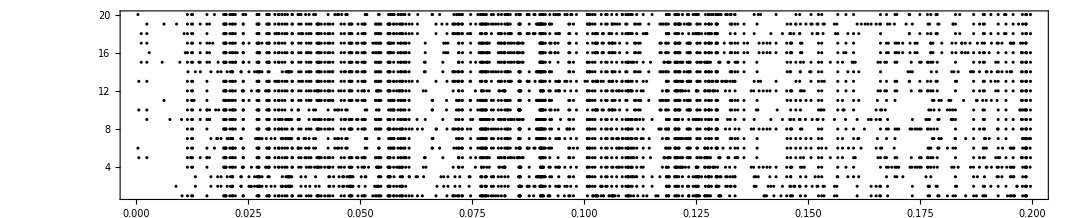

```mathematica
Show[Graphics[plotSNP[Range[nb],ConstantArray[Black,nb],0.002,popB20]],AspectRatio->0.2,Frame->True]
```

This shows genealogies at 0, 0.01, 0.02, 0.05, 0.20, on two different vertical scales. The first “escape” is just beyond 1cM, but the genealogy still retains the effects of the sweep out to 5cM or so:

```mathematica
hh[j_,ym_]:=Show[PlotGenealogy[genB20[[j]],NodeFunction->plotCoords[1]],PlotRange->{{-1,20},{0,ym}},Frame->True,FrameTicks->{None,Automatic},AspectRatio->0.7];
ii={1,6,22,87,-1};
GraphicsGrid[{hh[#,150]&/@ii,hh[#,800]&/@ii}]
ints20[[ii]]
```

-Graphics-

{{0,0.00116641},{0.00845516,0.0101709},{0.0199083,0.0203284},{0.049621,0.0504018},{0.199885,0.2}}

This shows all 30 of the “substantial” blocks

```mathematica
cf=ColorData["DarkRainbow"];gg[k_]:=Show[plotBranchFull[blB20⟦ppb[[k]]⟧,cf[(k-1)/Length[ppb]],sweepB20,0.2],Graphics[Prepend[Table[Disk[snpB20⟦ppb[[k]],j,{2,1}⟧,{0.001,3}],{j,Length[snpB20⟦ppb[[k]]⟧]}],Black]],PlotRange->{{0,0.2},{0,800}},AspectRatio->1,PlotLabel->"branch "~~ToString[ppb[[k]]]];
ListAnimate[Table[gg[k],{k,1,Length[ppb]}]]
```

#### Showing branches with many descendants

This is the set of branches used in the final figure

This shows the 9 branches with >8 descendants, that originate at or more recently than the mutation; and that have area >0.5. The branches with the largest area, longest extent,  and the most descendants tend to be near the sweep, but there are three small branches to the right with 9 or 10 descendants:

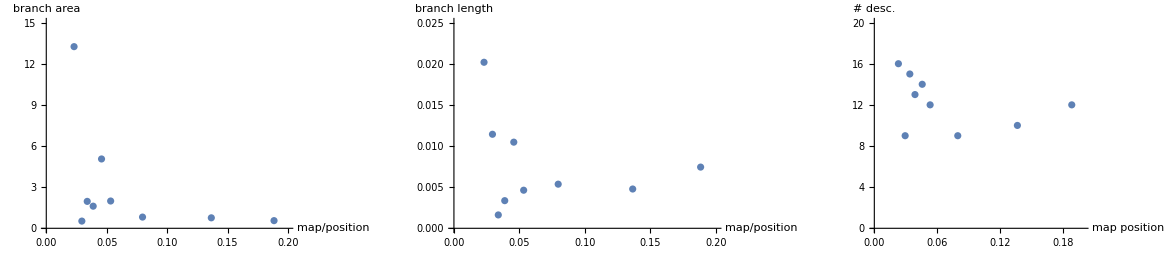

```mathematica
rn=Range[Length[blB20]];ba=branchAreaFull[sweepB20,0.2];
bx=Mean[Flatten[#[[3]]]]&/@blB20;blen=(#[[3,-1,-1]]-#[[3,1,1]])&/@blB20;
long=Select[rn,(Length[blB20[[#,1]]]>8)∧(blB20[[#,2]]≤101)∧(ba[[#]]>0.5)&];
GraphicsRow[{ListPlot[Transpose[{bx,ba}][[long]],AxesLabel->{"map/position","branch\narea"},PlotRange->{{0,0.2},{0,15}}],
ListPlot[Transpose[{bx,blen}][[long]],AxesLabel->{"map/position","branch\nlength"},PlotRange->{{0,0.2},{0,0.025}}],
ListPlot[Transpose[{bx[[long]],Length/@blB20[[long,1]]}],AxesLabel->{"map\nposition","# desc."},PlotRange->{{0,0.2},{0,20}}]}]
```

This shows the 20 branches with more than 5 descendants, area >0.5 and originating after the sweep.

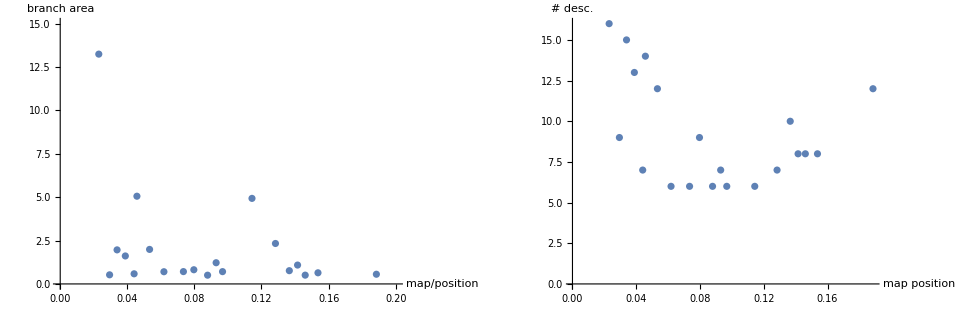

```mathematica
rn=Range[Length[blB20]];ba=branchAreaFull[sweepB20,0.2];bx=Mean[Flatten[#[[3]]]]&/@blB20;
long=Select[rn,(Length[blB20[[#,1]]]>5)∧(blB20[[#,2]]≤101)∧(ba[[#]]>0.5)&];
GraphicsRow[{ListPlot[Transpose[{bx,ba}][[long]],AxesLabel->{"map/position","branch\narea"},PlotRange->{{0,0.2},{0,15}}],
ListPlot[Transpose[{bx[[long]],Length/@blB20[[long,1]]}],AxesLabel->{"map\nposition","# desc."}]}]
```

This shows the 9 branches individually. They are typically narrow, consistent with having many descendants and therefore being prone to recombination.

```mathematica
cf=ColorData["DarkRainbow"];gg[k_]:=Show[plotBranchFull[blB20⟦long[[k]]⟧,cf[(k-1)/Length[long]],sweepB20,0.2],Graphics[Prepend[Table[Disk[snpB20⟦long[[k]],j,{2,1}⟧,{0.001,3}],{j,Length[snpB20⟦long[[k]]⟧]}],Black]],PlotRange->{{0,0.2},{0,800}},AspectRatio->1,PlotLabel->"branch "~~ToString[long[[k]]]~~" at "~~ToString[PaddedForm[blB20⟦long[[k]],3⟧,3]]];
ListAnimate[Table[gg[k],{k,1,Length[long]}]]
```

#### Making replicates

We wish to plot the time to MRCA for ~4 replicate sweeps, to superimpose on the focal sweep.  The ancestral genotype, prior to the mutation, is set to zero:

```mathematica
tMut=bounds[Reverse[selB]][[-1,1]];
Timing[time=0;Do[sweepB20rep[j]=makeC[20,0.2,400,selB];
sweepB20rep[j]=Join[sweepB20rep[j][[1;;tMut-1]],Replace[sweepB20rep[j][[tMut;;-1]],{1,x__}:>{0,x},{2}]],{j,4}];
Table[Length[sweepB20rep[j]],{j,4}]]
```

{131.056,{5369,2899,2560,2751}}

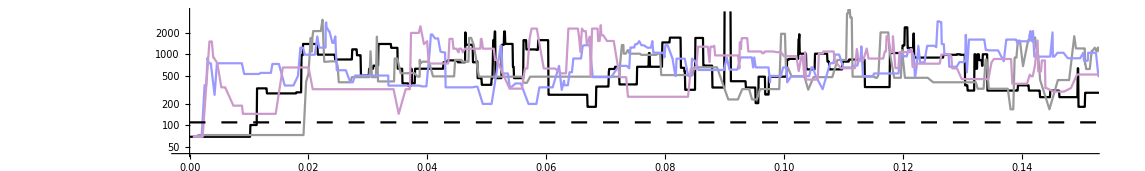

```mathematica
cols={Black,Blue,Purple,Brown};
dgf=genFunction[DepthOfGenealogy,x,genB20,ints20];
Show[LogPlot[dgf,{x,0,0.2},AspectRatio->0.15,PlotStyle->Black,PlotRange->{{0,0.15},{40,4000}}],
Table[ListLogPlot[Transpose[{Mean/@intervals[sweepB20rep[j],0.2],timeToMRCA[sweepB20rep[j],20,0.2]}],PlotStyle->Lighter[cols[[j]],0.6],AspectRatio->0.15,Joined->True],{j,3}],
LogPlot[110,{x,0,0.2},PlotStyle->{Black,Dashing[{0.01,0.01}]}]]
```

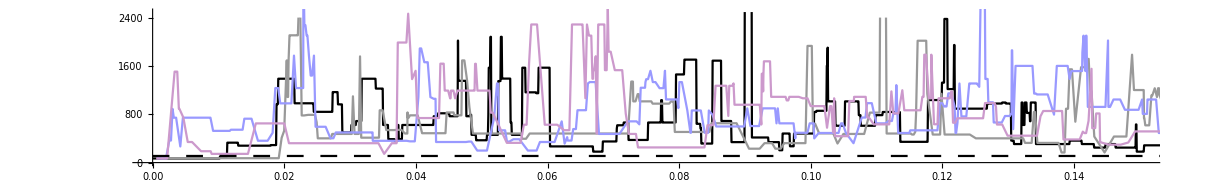

```mathematica
cols={Black,Blue,Purple,Brown};
dgf=genFunction[DepthOfGenealogy,x,genB20,ints20];
Show[Plot[dgf,{x,0,0.2},AspectRatio->0.15,PlotStyle->Black,PlotRange->{{0,0.15},{0,2500}}],
Table[ListPlot[Transpose[{Mean/@intervals[sweepB20rep[j],0.2],timeToMRCA[sweepB20rep[j],20,0.2]}],PlotStyle->Lighter[cols[[j]],0.6],AspectRatio->0.15,Joined->True],{j,3}],
Plot[110,{x,0,0.2},PlotStyle->{Black,Dashing[{0.01,0.01}]}]]
```

This saves the example: ancestry is enormous, apparently, so we did not save it. Note that there are two sets of genealogies: genB20 which includes only the sampled 20 genomes, and genB20New which includes the selected background and an outgroup. blB20 lists branches only from the first set. I do not save the genealogies, since these take a long time to construct, and are not needed for the plots. The ancestry stored here also includes ancestry for the main example.

```mathematica
Save["Big sweeps s=0.1, 2N=400 R=0.2 20 genomes reps 4 Jan",{sweepB20rep,ints20rep}];
```

```mathematica
<<"Big sweeps s=0.1, 2N=400 R=0.2 20 genomes reps 4 Jan";
```

#### Making the figure

This takes a while,  starting from the initialisation plus saved data:

```mathematica
rn=Range[Length[blB20]];ba=branchAreaFull[sweepB20,0.2];bx=Mean[Flatten[#[[3]]]]&/@blB20;
long=Select[rn,(Length[blB20[[#,1]]]>8)∧(blB20[[#,2]]≤101)∧(ba[[#]]>0.5)&];
```

Allele frequency reaches 0.9, 0.5, 0.1,  1/400 at 22, 29, 38, 53, 100, 110 generations back. One could draw dashed lines at these positions:

```mathematica
110-pos[Take[selB,-110]/400,#]&/@{0.9,0.5,0.1,0.0024}
```

{22,38,53,110}

This makes the genealogy plots:

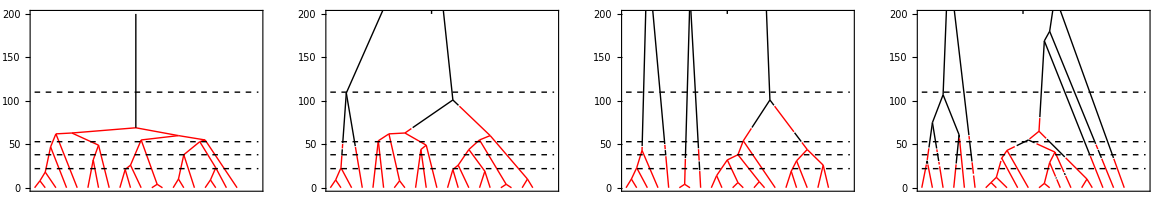

{{0,0.00116641},{0.0129117,0.0129652},{0.0524607,0.0525217},{0.197523,0.198033}}

```mathematica
mx=200;
hh[j_]:=Module[{mg},
mg=MakeGenealogyPlot[genB20New[[j,3,2]]];xy=plotCoords[1][0,mg[[2]]];
Show[PlotGenealogy[mg,MakeGenealogyPlot->False,NodeLabels->None,LeafLabels->None,NodeFunction->plotCoords[1],
BranchGraphic->mosaicBranch[mg,sweepB20,ints20[[j]],0.2,{{Black},{Red}}]],
Graphics[{Black,Line[{xy,{xy[[1]],mx}}]}],(* vertical branch back from the root *)
Graphics[Join[{Black,Dashing[{0.01,0.01}]},Line[{{0,#},{21,#}}]&/@{110,53,38,22}]],
Frame->True,FrameTicks->{None,Automatic},PlotRange->{{0,21},{0,mx}},AspectRatio->0.7]];
ii={1,10,100,420};
genPlot=GraphicsRow[hh/@ii]
ints20[[ii]]
```

```mathematica
cf=ColorData["DarkRainbow"];cols=cf/@Range[1,0,-1/(Length[long]-1)];nb=Length[snpB20];
gb[b_,c_]:=Show[plotBlockFull[blB20[[b]],Lighter[c,0.7],sweepB20,0.2],Graphics[{c,PointSize[0.005],plotSNP[b,popB20]}],PlotRange->{{0,0.21},{0,21}}];
cr=coalescedRegions[sweepB20[[70]],20,0.2];
snpPlot=Show[Graphics[plotSNP[Complement[Range[nb],long],ConstantArray[Gray,nb],0.003,popB20]],
MapThread[gb,{long,cols}],
Graphics[Join[{Opacity[0.3,Magenta]},Rectangle[{#[[1]],0},{#[[2]],20}]&/@cr]],AspectRatio->0.2,Frame->True];
dgf=genFunction[DepthOfGenealogy,x,genB20,ints20];
pwf=genFunction[MeanPairwiseDivergence,x,genB20,intervals[sweepB20,0.2]];
```

```mathematica
GraphicsColumn[{genPlot,
snpPlot,
LogPlot[pwf,{x,0,0.2},AspectRatio->0.15,PlotRange->{{0,0.2},{40,4000}}],
LogPlot[dgf,{x,0,0.2},AspectRatio->0.15,PlotRange->{{0,0.15},{40,4000}}]}]
```

-Graphics-

Figure. The top row shows four genealogies, at map positions 0, 0.013, 0.053, 0.198; the leftmost genealogy is at the selected locus. Red indicates lineages associated with the fitter allele, and black the ancestral allele; all lineages must recombine onto the ancestral (black) background by the time of the sweeping mutation, 110 generations into the past.  I have not got the colouring of the lines quite right yet.  The top left panel shows the (log) frequency of the sweeping allele on the same timescale. It could be better to drop this panel, and instead draw horizontal dashed lines on the genealogies at times 110,53,38,22, when p=1/400, 0.1, 0.5, 0.9.   The second row shows the 20 genomes, highlighting the 9 branches that have more than 8 descendants, that formed by coalescence more recently than the sweeping mutation, and that have areas >0.5.  The magenta block at the right shows the region linked to the selected locus, that coalesces in a single common ancestor at generation 69, just after the sweeping mutation arose.  Grey dots show SNP that are not on these 9 highlighted branches.  Note that there is some diversity within the magenta area, due to mutation subsequent to the sweep.  The third row shows mean pairwise divergence, and the fourth row the time back to the MRCA, bith on a log scale.

{{0,0.00116641},{0.0129117,0.0129652},{0.0524607,0.0525217},{0.197523,0.198033}}

## Definitions

### Generating the sweep trajectory

#### makeReps

```mathematica
makeReps::usage="makeReps[s,k_max,n_reps,seed] stores n_repsbranching processes, with a Poisson distribution of offspring, stopping at k_max, conditioned on establishment";
makeReps[s_,kmax_,nreps_,seed_]:=makeReps[s,kmax,nreps,seed]=Module[{bp={},np},
rep=0;
While[rep<nreps,
np=NestWhileList[RandomInteger[PoissonDistribution[ # (1+s)]]&,1,(0<#<kmax)&];
If[Last[np]>0,rep+=1;AppendTo[bp,np]]];
bp];
```

#### makeRepsFix

```mathematica
makeRepsFix::usage="makeReps[s,2N,n_reps,seed] stores n_repstrajectories, with a Wright-Fisher model, stopping at k_max, and conditioned on fixation";
makeRepsFix[s_,n_,nreps_,seed_]:=makeRepsFix[s,n,nreps,seed]=Module[{bp={},np},
rep=0;
While[rep<nreps,
np=NestWhileList[RandomInteger[BinomialDistribution[n, (#/n) (1+s)/(1+s (#/n))]]&,1,(0<#<n)&];
If[Last[np]>0,rep+=1;AppendTo[bp,np]]];
bp];
```

### Simulating the ARG, conditional on a sweep

#### coalesce

```mathematica
coalesce::usage="coalesce[{{1},{2,3},{4}},k]  iterates back one generation, assuming population size k. coalesce[{{1},{2,3}},{4},k] adds lineage {4} to the current set of families, assuming that the population is size k";
coalesce[pop_List,k_Integer]:=Fold[coalesce[#1,#2,k]&,{},pop];
coalesce[pop_List,x_List,k_Integer]:=Module[{j=Length[pop]},
If[Random[]<j/k,
MapAt[Join[#,x]&,pop,RandomInteger[{1,j}]],
Append[pop,x]]];
```

#### recombine

```mathematica
recombine::usage="recombine[{{{1},{2},…},{{6},{7},…}},r,p] allows for recombination at rates rq from Q to P, and rp from P to Q.";
recombine[{xq_List,xp_List},r_,p_]:=Module[{xxq,xxp},
xxq=RandomVariate[BernoulliDistribution[r p],Length[xq]];
xxp=RandomVariate[BernoulliDistribution[r(1-p)],Length[xp]];
{Join[Pick[xq,xxq,0],Pick[xp,xxp,1]],
Join[Pick[xq,xxq,1],Pick[xp,xxp,0]]}];
```

#### iterBack

```mathematica
iterBack::usage="iterBack[{{{1},{2},…},{{6},{7},…}},r,2N,k] iterates back one generation, with recombination & then coalescence.";
iterBack[{xq_List,xp_List},r_,n_,k_]:=MapThread[coalesce,{recombine[{xq,xp},r,k/n],{n-k,k}}];
```

#### iterC

```mathematica
iterC::usage="iterC[{{X,{j_1,…},{a_1,…}},…},R,2N,k] iterates back one generation, in a population of 2N with k copies of X=1.  iterC[{{X,{j_1,…},{a_1,…}},…},R,2N] iterates back one generation, with only background zero. The map length is R<1 with at most one crossover, probability R";
iterC[pop:{{(0|1),_List,_List}..},R_,n_Integer]:=iterC[pop,R,n,0];
iterC[pop:{{(0|1),_List,_List}..},R_,n_Integer,k_Integer]:=
Module[{ng=Length[pop],nr,bp,Y,recInds,repRules,j,npop,npop0,npop1,jj0,jj1},
nr=RandomInteger[BinomialDistribution[ng,R]];
bp=RandomReal[{0,R},nr];recInds=RandomSample[Range[ng],nr];Y=RandomInteger[BernoulliDistribution[k/n],nr];
repRules=MapThread[(#1->recombineC[pop⟦#1⟧,#2,#3])&,{recInds,Y,bp}];
npop=Flatten[ReplacePart[List/@pop,repRules],1];
npop0=Cases[npop,{0,_,_}];npop1=Cases[npop,{1,_,_}];
jj0=RandomInteger[{1,n-k},Length[npop0]];
jj1=RandomInteger[{1,k},Length[npop1]];
condense/@DeleteCases[Join[
coalesceC[npop0⟦Flatten[Position[jj0,#]]⟧]&/@Union[jj0],
coalesceC[npop1⟦Flatten[Position[jj1,#]]⟧]&/@Union[jj1]],{_,_,{{}...}}]];
```

#### makeC

```mathematica
makeC::usage="makeC[n,R,2N] simulates coalescence of n genes in a population of size 2N, on map length R; merges adjacent blocks with the same ancestry, and deletes non-ancestral lineages.  makeC[n,R,2N,{j_1,…}] simulates a selective sweep with j_i copies in each generation; sampled lineages all carry the fitter allele. Simulates back until complete coalescence. time and nGenes can be used to track.";
makeC[n_Integer,R_,n2_Integer]:=Module[{i,pop0},
pop0=Table[{0,{},{{i}}},{i,n}];
deleteNA[condense/@#]&/@NestWhileList[(time+=1;nGenes=Length[#1];
iterC[#1,R,n2])&,pop0,Not[coalescedQ[#,n]]&]];
makeC[n_Integer,R_,n2_Integer,nsel_List]:=Module[{i,pop0},
pop0=Table[{1,{},{{i}}},{i,n}];time=0;
deleteNA[condense/@#]&/@FoldWhileList[(time+=1;nGenes=Length[#1];
iterC[#1,R,n2,#2])&,pop0,Reverse[nsel],(Not[coalescedQ[#,n]]∧(time<Length[nsel]))&]];
```

#### deleteAllNC

```mathematica
deleteAllNC::usage="deleteAllNC[{{X,{j_1,…},{a_1,…}},…}]  deletes tips and merges blocks that have the same ancestry";
deleteAllNC[pop:{{_,_List,_List}...}]:=deleteAllNC/@pop;
deleteAllNC[{X:(0|1),jl_List,al_List}]:=Module[{jal},
jal=Transpose[Transpose[{Prepend[jl,0],al}]/.{{x_,{_}}:>{x,{}}}];
condense[{X,Drop[jal⟦1⟧,1],jal⟦2⟧}]];
```

#### deleteNC

```mathematica
deleteNC::usage="deleteNC[{{X,{j_1,…},{a_1,…}},…}] deletes lineages that are not coalesced ";
deleteNC[pop:{{_,_List,_List}...}]:=Select[pop,(Max[Length/@#⟦3⟧]>1)&];
```

Note: this definition is used in “HH revisiited” and deletes  tips.

#### deleteNA

```mathematica
deleteNA::usage="deleteNA[{{X,{j_1,…},{a_1,…}},…}] deletes lineages that are not ancestral ";
deleteNA[pop:{{_,_List,_List}...}]:=Select[pop,(Max[Length/@#⟦3⟧]≥1)&];
```

This keeps the tips.

#### condense

```mathematica
condense::usage="condense[{X,{j_1,j_2,…},{a_1,…}}] merges segments that have the same ancestry";
condense[{X_,jl_List,al_List}]:=Module[{jal=Transpose[{Prepend[jl,0],al}]},
jal=Transpose[jal//.{x___,{y_,a_},{_,a_},z___}:>{x,{y,a},z}];
{X,Drop[jal⟦1⟧,1],jal⟦2⟧}];
```

#### coalesceC

```mathematica
coalesceC::usage="coalesceC[{{X,{j_1,…},{{1,2},…}},{X,{j_1^*,…},{{3,4},…}},…}] produces a single coalesced genome, merging junctions and ancestries. More than two genomes may coalesce.";
coalesceC[g:{{X:(0|1),_List,_List}...}]:=Module[{jt=Union@@g⟦All,2⟧},
{X,jt,(Union@@#)&/@Transpose[MapThread[splitAncestry[#1,#2,jt]&,Transpose[g⟦All,{2,3}⟧]]]}];
```

#### splitAncestry

```mathematica
splitAncestry::usage="splitAncestry[{j_1,j_2,…},{a_1,a_2,…},{j_1^*,j_2^*,…}] extends the list {a_1,a_2,…} by duplicating elements that contain new junctions; j^* lists all junctions. ";
splitAncestry[j1_List,a1_List,j2_List]:=Module[{nn},
nn=1+BinCounts[(1+pos[j1,#])&/@Complement[j2,j1],{1,Length[a1]+1}];
Flatten[MapThread[ConstantArray,{a1,nn}],1]];
```

#### recombineC

```mathematica
recombineC::usage="recombineC[{X,{j_1,…},{{1,2},…},Y,θ] generates two ancestral genomes, breakpoint θ; the partner genome is in state Y, and is assumed non-ancestral";
recombineC[{X:(0|1),jl_List,al_List},Y:(0|1),θ_]:=Module[{pp=pos[jl,θ]},
{{X,Append[jl⟦1;;pp⟧,θ],Append[al⟦1;;(pp+1)⟧,{}]},
{Y,Prepend[jl⟦pp+1;;-1⟧,θ],Prepend[al⟦(pp+1);;-1⟧,{}]}}];
```

### Adding SNP to the ARG

#### makeSNP

```mathematica
makeSNP::usage="makeSNP[{{t,{r_0,r_1}}…},μ/r] draws SNP at rate μ/r per map length. The SNP are output as {t,r}, their time of origin and genomic location. The block positions {{t,{r_0,r_1}}…} are generated by posBlock[pop,branch,R]";
makeSNP[posns:{{_Integer,{_,_}}...},μr_]:=Flatten[makeSNP[#,μr]&/@posns,1];
makeSNP[{t_Integer,{r0_,r1_}},μr_]:=Module[{nm},
nm=RandomInteger[PoissonDistribution[μr (r1-r0)]];
{t,#}&/@RandomReal[{r0,r1},nm]];
```

#### addSNP

```mathematica
addSNP::usage="addSNP[{{b_1,k_1},…},{{{t_(1, 1),x_(1, 1)},…},…}] generates an array genomes×SNP, in the form {{t_1,x_1,k_1},…} where k indexes the branch, in the given order (as generated by branchList). addSNP[pop,μ/r,R] sets up a full array of randomly generated SNP.";
addSNP[br_List,snp_List]:=Module[{pop,k,n=Max[Flatten[First/@br]]},
pop=ConstantArray[{},n];
Do[(pop=Insert[pop,snp⟦k⟧/.{{t_Integer,x_}:>{t,x,k}},br⟦k,1⟧/.{j_Integer:>{j,-1}}]),{k,Length[snp]}];
pop=Flatten[#,1]&/@pop];
addSNP[pop_List,μr_,R_]:=Module[{br=branchList[pop]},
addSNP[br,makeSNP[posBlock[pop,#⟦1⟧,R],μr]&/@br]];
```

#### addSNPFull

```mathematica
addSNPFull::usage="addSNPFull[{{b_1,k_1},…},{{{t_(1, 1),x_(1, 1)},…},…}] generates an array genomes×SNP, in the form {{t_1,x_1,k_1},…} where k indexes the branch, in the given order (as generated by branchListFull). addSNPFull[pop,μ/r,R] sets up a full array of randomly generated SNP.";
addSNPFull[pop_List,μr_,R_]:=Module[{br=branchListFull[pop,R]},
addSNP[br,makeSNP[posBlockFull[pop,#⟦1⟧,R],μr]&/@br]];
```

#### winSNP

```mathematica
winSNP::usage="winSNP[pop,{r_0,r_1}] selects the SNP present within this window, in the form {{{t_1,x_1,b_1},…},…}"; 
winSNP[pop_List,w_List]:=Module[{f},
f[s_]:=Between[s[[2]],w];
Select[#,f]&/@pop];
```

#### nsSNP, piSNP, nsHapSNP, piHapSNP

```mathematica
nsSNP::usage="nsSNP[pop] gives the # of segregating sites for this window";
nsSNP[pop_List]:=Length[Union[Flatten[pop,1]]];
```

```mathematica
piSNP::usage="piSNP[pop] gives π for this window, calculated as the sum of 2pq over segregating sites";
piSNP[pop_List]:=Module[{kk,n=Length[pop]},
kk=Last/@Tally[Flatten[pop,1]];Total[2 kk/n(1-kk/n)]];
```

```mathematica
nsHapSNP::usage="nsHapSNP[pop] gives the # of haplotypes for this window";
nsHapSNP[pop_List]:=Length[Union[pop]];
```

```mathematica
piHapSNP::usage="piSNP[pop] gives π for this window, calculated from the # of haplotypes";
piHapSNP[pop_List]:=Module[{xx,n=Length[pop]},
xx=Last/@Tally[pop];1.-Total[(xx/n)^2]];
```

#### snpSel, snpTally, hapsTally, nHaps, nSites, snpPi

```mathematica
snpSel::usage="snpSel[pop,{r_0,r_1}] gives the SNP in this window";
snpSel[ind:{{_Integer,_,_Integer}...},{r0_,r1_}]:=Select[ind,(r0<=#[[2]]<r1)&];
snpSel[pop:{{{_Integer,_,_Integer}...}...},{r0_,r1_}]:=snpSel[#,{r0,r1}]&/@pop;
```

```mathematica
snpTally::usage="snpTally[pop] takes a set of genotypes, and finds the SNP & the # of copies, in sorted order";
snpTally[pop_List]:=Sort[Tally[Flatten[pop,1]]];
hapsTally::usage="hapsTally[pop] takes a set of genotypes, and finds the  # of each haplotype, in sorted order";
hapsTally[pop_List]:=Tally[Sort/@pop];
```

```mathematica
nHaps::usage="nHaps[pop] ggives the # of haplotypes";
nHaps[pop_List]:=Length[hapsTally[pop]];
```

```mathematica
nSites::usage="nSites[pop] gives the # of segregating sites";
nSites[pop_List]:=Length[Union[Flatten[pop,1]]];
```

```mathematica
snpPi::usage="snpPi[pop] gives π, as ∑2pq";
snpPi[pop_List]:=Module[{sfs,n=Length[pop]},Total[2 sfs(2n0-sfs)/n^2]];
```

### Describing the ARG

#### findBlocks

```mathematica
findBlocks::usage="findBlocks[k,{X,{j_1,…},{a_1,…}}] finds the blocks ancestral to k";
findBlocks[k_,{X_,j_,a_}]:=Module[{al=condense[{X,j,If[MemberQ[#,k],{k},{}]&/@a}]},
If[al⟦3,1⟧=={k},Partition[Prepend[al⟦2⟧,0],2],Partition[al⟦2⟧,2]]];
```

#### findAllBlocks

```mathematica
findAllBlocks::usage="findAllBlocks[k,{{X,{j_1,…},{a_1,…}},...}] finds all blocks ancestral to k, in the form {…,{{j_1,j_2},i},…}, where i is the position in the supplied list of ancestral genomes";
findAllBlocks[k_,pop:{{_,_,_}...}]:=Module[{fb},
fb=MapIndexed[{findBlocks[k,#1],#2}&,pop];
Sort[Flatten[fb/.{{b:{{_,_}...},{i_}}:>({#,i}&/@b)},1]]];
```

#### plotAncestry

```mathematica
plotAncestry::usage="Graphics[plotAncestry[n,{{X,{j_1,…},{a_1,…}},...},cf]] plots the ancestry of genomes 1…n using ColorFunction cf. ";
plotAncestry[n_Integer,pl_List,cf_]:=Module[{na=Length[pl],k},
Flatten[Table[findAllBlocks[k,pl]/.{{x0_,x1_},i_Integer}:>{cf[i/na],Rectangle[{x0,k-1/2},{x1,k+1/2}]},{k,n}],2]];
```

#### coalescedQ

```mathematica
coalescedQ::usage="coalescedQ[{{X,{j_1,…},{a_1,…}},…},n] determines whether all genealogies have coalesced; n is the sample size. Can also be applied to a single genome";
coalescedQ[lin:{(0|1),_List,_List},n_Integer]:=Min[DeleteCases[Length/@lin⟦3⟧,0]]==n;
coalescedQ[pop:{{(0|1),_List,_List}..},n_Integer]:=And@@(coalescedQ[#,n]&/@pop);
```

#### branchList

```mathematica
branchList::usage="branchList[{{{X,{..},{..}},..},..}] tallies the branches, returning {{branch,#},…}. Ancestor->True includes the branches ancestral to all genomes (an artefact?). Tips->False does not include the tip branches. Stores results.";
Ancestor::usage="Ancestor is an option for branchList that determines whether the 'branch' ancestral to all is included.";
Tips::usage="Tips is an option for branchList that determines whether tip branches are included.";
Options[branchList]={Ancestor->False,Tips->True};
branchList[pop_List,opts___Rule]:=branchList[pop,opts]=
Module[{anc=Ancestor/.{opts}/.Options[branchList],tps=Tips/.{opts}/.Options[branchList],bl},
bl=Tally[Sort/@DeleteCases[Flatten[pop⟦All,All,3⟧,2],{}]];
If[Not[anc],bl=Select[bl,Length[#[[1]]]<Length[pop[[1]]]&]];
If[Not[tps],Select[bl,(Length[#[[1]]]>1)&],bl]];
```

#### posBlock

```mathematica
posBlock::usage="posBlock[{{{X,{j_1,…},{…}},…},…},{2,13,…},R] returns the generations and blocks covered by this branch, in the form {…,{t,{{r_1,r_2},…},…}. posBlock[{{{X,{j_1,…},{…}},…},…},R] stores all the positions, using branchList[]. Options can be supplied.";
posBlock[pop:{{{(0|1),_List,_List}..}..},R_,opts___Rule]:=posBlock[pop,R,opts]=
posBlock[pop,#⟦1⟧,R]&/@branchList[pop,opts];
posBlock[pop:{{{(0|1),_List,_List}..}..},br_List,R_]:=Module[{posn=Position[pop,br]},
{#⟦1⟧,int[#⟦4⟧,pop[[#⟦1⟧,#⟦2⟧,2]],R]}&/@posn];
```

#### branchListFull, posBlockFull, tallyIntervalNumber

```mathematica
branchListFull::usage="branchListFull[{{{X,{..},{..}},..},..},R]returns {{S,t,{{r_1,r_2},…}},…}, where S is the set of descendant lineages, and t is the coalescence time when this branch was generated. Stores results.  Blocks are defined as bringing together a set S and starting at time t; they may be on disjunct intervals.";
branchListFull[pop_List,R_]:=branchListFull[pop,R]=
Module[{tts,iv,ints=intervals[pop,R],bl=branchList[pop],j,ct},
tts=timeSpans[pop,#,R]&/@ints;
Flatten[Table[
(ct=Union[DeleteCases[tts⟦All,j⟧,{}]⟦All,1⟧];
(* One must make sure that only the first entry in timeSpans is searched *)
(iv=List@@(IntervalUnion@@(Interval/@(ints⟦Position[tts⟦All,j⟧/.{a_Integer,b_Integer}->{a},#]⟦All,1⟧⟧)));
{bl⟦j,1⟧,#,iv})&/@ct),{j,Length[bl]}],1]];
```

branchListFull identifies branches as having begun at a specific time, and bringing together a certain set of lineages.  It would still conflate branches that are formed at exactly the same time, between exactly the same set of lineages, but by different coalescence events. However, this seems unlikely (and becomes vanishingly rare as N increases, and we approach the coalescent limit). The opposite problem is more of a concern: the algorithm must allow for the possibility that a single coalescence event brings together multiple clusters of lineages, so that the branch occupies disjunct regions.  Hence, the intervals that describe a branch are given in the form {{r_1,r_2}…}.  This will usually contain a single interval - which can be checked by tallyIntervalNumber[].

```mathematica
tallyIntervalNumber::usage="tallyIntervalNumber[{{S,t,{{r_1,r_2},…}},…}] tallies the numbers of intervals occupied by each branch. This will usually be 1, but sometimes a single coalescence event can generate co-ancestry in disjunct regions.";
tallyIntervalNumber[bl:{{_List,_Integer,_List}...}]:=Tally[Length/@bl[[All,3]]];
```

```mathematica
posBlockFull::usage="posBlockFull[{{{X,{j_1,…},{…}},…},…},{{2,13,…},t,{{r_1,r_2}},R] stores the generations and blocks covered by this branch, in the form {…,{t,{{r_1,r_2},…},…}. posBlockFull[{{{X,{j_1,…},{…}},…},…},R] stores all the positions, using branchList[]. Options can be supplied.";
posBlockFull[pop:{{{(0|1),_List,_List}..}..},R_]:=posBlockFull[pop,R]=
posBlockFull[pop,#,R]&/@branchListFull[pop,R];
posBlockFull[pop:{{{(0|1),_List,_List}..}..},br_List,R_]:=Module[{ints,pbf},
ints=(List@@(IntervalIntersection[Interval@@br[[3]],Interval[#[[2]]]]/.
{Interval[{x_,y_}]:>If[Abs[y-x]<10^-8,Interval[],Interval[{x,y}]]}))&/@posBlock[pop,br[[1]],R];
pbf=Transpose[{Pick[posBlock[pop,br[[1]],R],Not[#=={}]&/@ints][[All,1]],DeleteCases[ints,{}]}];
Flatten[pbf/.{{t_Integer,iv_List}:>({t,#}&/@iv)},1]];
```

posBlockFull returns a flat list in the form {{t,{r_1,r_2}},…}, which gives every instance of the block. The block may have disjunct regions, which will all be included.  One problem is that intervals that share an edge (i.e. Interval[{x,y}] and Interval[{y,z}]) are counted as overlapping by IntervalIntersection, giving Interval[{y,y}]. Such cases are removed.

#### branchAreaFull

```mathematica
branchAreaFull::usage="branchAreaFull[pop,branch,R] gives the 'area' of the branch, using posBlockFull. branchAreaFull[pop,R] stores all the areas.";
branchAreaFull[pop_List,br:{_List,_Integer,_List},R_]:=Total[posBlockFull[pop,br,R]/.{_Integer,{x0_,x1_}}:>(x1-x0)];
branchAreaFull[pop_List,R_]:=branchAreaFull[pop,R]=Total[#/.{_Integer,{x0_,x1_}}:>(x1-x0)]&/@posBlockFull[pop,R];
```

#### branchLength, branchWidth

```mathematica
branchLength::usage="branchLength[{{t,{r_0,r_1}},…} takes the list describing branch positions, as generated by posBlock, and finds the time spanned by the branch.";
branchLength[pb_List]:=Length[Union[pb⟦All,1⟧]];
```

```mathematica
branchWidth::usage="branchWidth[{{t,{r_0,r_1}},…} takes the list describing branch positions, as generated by posBlock, and finds the mean map width spanned by the branch.";
branchWidth[pb_List]:=Mean[pb⟦All,2⟧.{-1,1}];
```

#### firstTimes, lastTimes

```mathematica
firstTimes::usage="firstTimes[pop,{r_0,r_1},R] gives the times when branches begin";
firstTimes[pop_List,intv:{_,_},R_]:=Union[Flatten[First/@DeleteCases[timeSpans[pop,intv,R],{}]]];
lastTimes::usage="lastTimes[pop,{r_0,r_1},R] gives the times when branches end";
lastTimes[pop_List,intv:{_,_},R_]:=Union[Flatten[Last/@DeleteCases[timeSpans[pop,intv,R],{}]]];
```

#### junctions, intervals

```mathematica
junctions::usage="junctions[pop,R] stores a list of all the junctions";
junctions[pop_List,R_]:=junctions[pop,R]=Module[{pbl},
pbl=posBlock[pop,#⟦1⟧,R]&/@branchList[pop];
Union[Flatten[pbl[[All,All,2]]]]];
```

```mathematica
intervals::usage="intervals[pop,R] gives the intervals between junctions.";
intervals[pop_List,R_]:=Module[{jj=junctions[pop,R]},
Transpose[{Drop[jj,-1],Drop[jj,1]}]];
```

#### timeSpans, branchesPresent

```mathematica
timeSpans::usage="timeSpans[pop,{r_0,r_1},R] returns the time spanned by the branches in this interval, in a list that corresponds to branchList[pop]. Options can be supplied.";
timeSpans[pop_List,intv:{_,_},R_,opts___Rule]:=Module[{j,tt,pbl=posBlock[pop,R,opts],cQ},
tt=Table[Select[pbl[[j]],overlapQ[intv,#[[2]]]&]⟦All,1⟧,{j,Length[pbl]}];
cQ=And@@(If[#=={},True,Length[#]==Length[Range[#[[1]],#[[-1]]]]]&/@tt);
If[cQ,Replace[tt,{{t0_,___,t1_}:>{t0,t1}},{1}],
Message["Branches are not present for a set of consecutive times: `1`",tt];$Failed]];
```

```mathematica
branchesPresent::usage="branchesPresent[pop,{r_0,r_1},R] gives the branches present in an interval";
branchesPresent[pop_List,intv:{_,_},R_,opts___Rule]:=Module[{ts=timeSpans[pop,intv,R,opts]},
Pick[Range[Length[ts]],Length[#]>0&/@ts]];
```

#### timeSpansFull, branchesPresentFull

```mathematica
timeSpansFull::usage="timeSpansFull[pop,{r_0,r_1},R] stores the time spanned by the branches in this interval, in a list that corresponds to branchListFull[pop]. Options can be supplied.";
timeSpansFull[pop_List,intv:{_,_},R_,opts___Rule]:=timeSpansFull[pop,intv,R,opts]=
Module[{j,tt,pbl=posBlockFull[pop,R,opts],cQ},
tt=Table[Select[pbl[[j]],overlapQ[intv,#[[2]]]&]⟦All,1⟧,{j,Length[pbl]}];
cQ=And@@(If[#=={},True,Length[#]==Length[Range[#[[1]],#[[-1]]]]]&/@tt);
If[cQ,Replace[tt,{{t0_,___,t1_}:>{t0,t1},{t0_}:>{t0,t0}},{1}],
Message["Branches are not present for a set of consecutive times: `1`",tt];$Failed]];
```

```mathematica
branchesPresentFull::usage="branchesPresentFull[pop,{r_0,r_1},R] gives the branches present in an interval";
branchesPresentFull[pop_List,intv:{_,_},R_,opts___Rule]:=Module[{ts=timeSpansFull[pop,intv,R,opts]},
Pick[Range[Length[ts]],Length[#]>0&/@ts]];
```

#### ancestralBranches, descendantBranches

```mathematica
ancestralBranches::usage="ancestralBranches[tip,pop] lists the branches ancestral to the tip, tracing back through time. Branches are indexed according to branchList[pop].";
ancestralBranches[tip_Integer,pop_List]:=Intersection[brX,Flatten[Position[branchList[pop]⟦All,1⟧,{___,tip,___}]]];
```

```mathematica
descendantBranches::usage="descendantBranches[t,pop,interval,R] lists the branches that descend from each coalescence event at time t; indices correspond to branchList[pop]";
descendantBranches[t_Integer,pop_List,intv:{_,_},R_]:=
Module[{j,tts=timeSpans[pop,intv,R],pose,posN,bl=branchList[pop]},
posN=Flatten[Position[tts,{t,___}]];posE=Flatten[Position[tts,{___,t-1}]];
Table[Select[posE,SubsetQ[bl[[posN[[j]],1]],bl[[#,1]]]&],{j,Length[posN]}]];
```

#### ancestralBranchesFull, descendantBranchesFull

```mathematica
(*BROKEN
ancestralBranchesFull::usage="ancestralBranchesFull[tip,pop] lists the branches ancestral to the tip, tracing back through time. Branches are indexed according to branchListFull[pop].";
ancestralBranchesFull[tip_Integer,pop_List]:=Intersection[branchesPresent[pop,intervals[pop,R][[10]],0.1],Flatten[Position[branchListFull[pop]⟦All,1⟧,{___,tip,___}]]];*)
```

```mathematica
descendantBranchesFull::usage="descendantBranchesFull[t,pop,interval,R] lists the branches that descend from each coalescence event at time t; indices correspond to branchListFull[pop]";
descendantBranchesFull[t_Integer,pop_List,intv:{_,_},R_]:=
Module[{j,tts=timeSpansFull[pop,intv,R],pose,posN,bl=branchListFull[pop,R]},
posN=Flatten[Position[tts,{t,___}]];posE=Flatten[Position[tts,{___,t-1}]];
Table[Select[posE,SubsetQ[bl[[posN[[j]],1]],bl[[#,1]]]&],{j,Length[posN]}]];
```

#### overlapQ, consecutiveQ

```mathematica
consecutiveQ::usage="consecutiveQ[{2,3,4}] checks whether the list is of consecutive integers, or is empty.  Integers can repeat.";
consecutiveQ[x:{}]:=True;
consecutiveQ[x:{__Integer}]:=Module[{ux=Union[x]},(Length[ux]==(ux[[-1]]-ux[[1]]+1))];
```

```mathematica
overlapQ::usage="overlapQ[{x_0,x_1},{r_0,r_1}] determines whether these intervals overlap.";
overlapQ[{x0_,x1_},{y0_,y1_}]:=(x1>y0∧x0<y1)(*Not[Interval[]===IntervalIntersection[Interval[{x0,x1}],Interval[{y0,y1}]]]*);
```

My first scheme failed, because it counted adjacent intervals as overlapping. The current formulation avoids this.

#### condenseNewick, makeNewick

```mathematica
condenseNewick::usage="condenseNewick[g] condenses information from a genealogy, in the form Node[i,{t,{}},{Node[…],…}], to the form Node[i,Δt,{Node[…],…}], where Δt is the branch length.";
condenseNewick[g_Node]:=Module[{ff},
ff[nl_List,tp_Integer]:=Replace[nl,{Node[j_,{t_Integer,{}},nl2_List]:>Node[j,{t,tp-t,{}},nl2]},{1}];
Replace[g,{Node[i_,{tp_Integer,dt___,{}},nl_List]:>Node[i,{tp,dt,{}},ff[nl,tp]]},All]/.Node[i_,{t_,{}},nl_List]:>Node[i,0,nl]//.Node[i_,{t_,dt_,{}},nl_List]:>Node[i,dt,nl]];
```

```mathematica
makeNewick::usage="makeNewick[g] gives the Newick format for g as a string";
makeNewick[g_Node]:=Module[{ss},
ss=condenseNewick[g]//.Node[i_Integer,t_Integer,nl_List]:>Node[nl,ToString[i]~~":"~~ToString[t]]/.Node->List/.{{{},s_String}->s};
StringReplace[StringReplace[ToString[ss],{"{"->"(","}"->")"}],"),"->")"]];
```

#### coalescedRegions, timeToMRCA

```mathematica
coalescedRegions::usage="coalescedRegions[{{X,{r_1,r_2,…},{S_(0, 1),S_(1, 2),…}},…},n,R] gives the intervals that have completely coalesced. The first argument is a list of ancestry at some time in the past, i.e. a row in the ancestral graph";
coalescedRegions[anc_,n_Integer,R_]:=Append[Prepend[anc[[#[[1]],2]],0],R][[#[[3]]+{0,1}]]&/@Position[anc,Range[n]];
```

```mathematica
timeToMRCA::usage="timeToMRCA[pop,n,R] stores the time to MRCA of each of the intervals";
timeToMRCA[pop_,{r0_,r1_},n_Integer,R_]:=Position[ancestry[pop,{r0,r1},R],Range[n]][[1,1]];
timeToMRCA[pop_,n_Integer,R_]:=timeToMRCA[pop,n,R]=timeToMRCA[pop,#,n,R]&/@intervals[pop,R];
```

#### nestedQ, insideQ

```mathematica
nestedQ::usage="nestedQ[{S_1,t_1,{r_0,r_1}},{S_2,t_2,{r_0^*,r_1^*}}] returns True if S_1⊂S_2, t_1<t_2, and {r_0,r_1} is within {r_0^*,r_1^*}. nestedQ[{S_1,t_1,{r_0,r_1}},{{S_2,t_2,{r_0^*,r_1^*}},…}] returns True if the first branch is nested within any of the second list.  A branch cannot be nested within itself.";
nestedQ[{S1_List,t1_Integer,int1:{{_,_}...}},{S2_List,t2_Integer,int2:{{_,_}...}}]:=SubsetQ[S2,S1]∧(t1<t2)∧insideQ[int1,int2];
nestedQ[br1:{_List,_Integer,{{_,_}...}},br2l:{{_List,_Integer,{{_,_}...}}...}]:=Or@@(nestedQ[br1,#]&/@br2l);
```

```mathematica
insideQ::usage="insideQ[{r_0,r_1},{{r_0^*,r_1^*},…}] returns True if the interval {r_0,r_1} is inside one of the following list of intervals.insideQ[{{r_0,r_1},…},{{r_0^*,r_1^*},…}] returns True if all the intervals in the first list are within the second list.";
insideQ[{r0_?NumberQ,
r1_?NumberQ},rl:{{_?NumberQ,_?NumberQ}...}]:=Or@@((#[[1]]≤r0≤r1<=#[[2]])&/@rl);
insideQ[rl1:{{_?NumberQ,_?NumberQ}...},rl2:{{_?NumberQ,_?NumberQ}...}]:=And@@(insideQ[#,rl2]&/@rl1);
```

### Constructing genealogies from the ARG

#### makeGenealogy

```mathematica
makeGenealogy::usage="makeGenealogy[pop,interval,R] makes the genealogy for the given interval, which must not contain any junctions.";
makeGenealogy[pop_List,intv:{_,_},R_]:=Module[{
tts=timeSpans[pop,intv,R],
lastNodeIndex=Length[branchList[pop]]+1,
ngenes=Length[First[pop]],ct=DeleteCases[firstTimes[pop,intv,R],1],
g,j,posNew,descBranches,lastCoalTime},
If[validIntervalQ[pop,intv,R],
g=Table[Node[j,{0,{}},{}],{j,ngenes}];(*Set up the initial lineages*)
Do[posNew=Flatten[Position[tts,{ct⟦j⟧,___}]];
descBranches=descendantBranches[ct⟦j⟧,pop,intv,R];
MapThread[(g=updateGenealogy[g,#1,#2,ct⟦j⟧])&,{posNew,descBranches}],
{j,Length[ct]}];
lastCoalTime=Max[Flatten[tts]]+1;
Node[lastNodeIndex,{lastCoalTime,{}},g],
Message[makeGenealogy::badInterval,intv];$Failed]];
makeGenealogy::badInterval="Interval `1` contains junctions.";
```

#### makeGenealogyFull

```mathematica
makeGenealogyFull::usage="makeGenealogyFull[pop,interval,R] makes the genealogy for the given interval, which must not contain any junctions.";
makeGenealogyFull[pop_List,intv:{_,_},R_]:=Module[{
tts=timeSpansFull[pop,intv,R],
lastNodeIndex=Length[branchListFull[pop,R]]+1,
ngenes=Length[First[pop]],ct=DeleteCases[firstTimes[pop,intv,R],1],
g,j,posNew,descBranches,lastCoalTime},
If[validIntervalQ[pop,intv,R],
g=Table[Node[j,{0,{}},{}],{j,ngenes}];(*Set up the initial lineages*)
Do[posNew=Flatten[Position[tts,{ct⟦j⟧,___}]];
descBranches=descendantBranchesFull[ct⟦j⟧,pop,intv,R];
MapThread[(g=updateGenealogy[g,#1,#2,ct⟦j⟧])&,{posNew,descBranches}],
{j,Length[ct]}];
lastCoalTime=Max[Flatten[tts]]+1;
Node[lastNodeIndex,{lastCoalTime,{}},g],
Message[makeGenealogyFull::badInterval,intv];$Failed]];
makeGenealogy::badInterval="Interval `1` contains junctions.";
```

#### Checking ancestry

I think these checks worked out...

Identifying the ancestral genotype associated with each branch is not so straightforward.  Branches are defined as bringing together a specific set of genes at a specific time which (one hopes) is the same coalescence event.  In any coalescence event, two specific ancestral lineages merge, and they must have the same genotype at the selected locus.  However, tracing the branch further back, one can have recombination events, such that ancestry is no longer the same.  Therefore, branches are not necessarily of a uniform genotype, even if they are all ancestral to the same set of descendants.

This identifies the most complex case, where  branch 374 ({1,4,12}, t=174) appears in three disjunct intervals.

```mathematica
posn=Position[blB20,{_List,_Integer,{_,_,_}}];{posn,blB20[[posn[[1,1]]]]}
```

{{{347}},{{1,4,12},174,{{0.0823478,0.0840355},{0.0868214,0.0894669},{0.0899643,0.0922881}}}}

These are all the 6893 ancestors that carry this branch:

```mathematica
pp=Position[sweepB20,blB20[[347,1]]]
```

{{99,24,3,5},{100,29,3,5},{101,6,3,5},{102,17,3,5},{103,5,3,5},{104,7,3,5},{105,19,3,5},{106,18,3,5},{107,8,3,5},{108,28,3,5},{109,3,3,5},{110,7,3,5},{111,11,3,5},{112,13,3,5},{113,7,3,8},{114,22,3,8},{115,27,3,8},6859,{4255,20,3,4},{4256,12,3,4},{4257,12,3,4},{4258,18,3,4},{4259,9,3,4},{4260,14,3,4},{4261,10,3,4},{4262,16,3,4},{4263,16,3,4},{4264,13,3,4},{4265,17,3,4},{4266,10,3,4},{4267,24,3,4},{4268,2,3,4},{4269,27,3,4},{4270,4,3,4},{4271,18,3,4}}
 |  |  |  |

This transforms the information into {{r_0,r_1},X} for each ancestor in block 347, and takes the union. There are many intervals involved, but surprisingly, there is one interval {0899501,0.0899643} (interval 193) that has both ancestral genotypes.  How can this happen?

```mathematica
intv=intervals[sweepB20,0.2];
rxl={Append[Prepend[sweepB20[[#[[1]],#[[2]],2]],0],0.2][[{-1,0}+#[[4]]]],sweepB20[[#[[1]],#[[2]],1]]}&/@pp;
urxl=Union[rxl]
```

{{{0,0.082638},0},{{0,0.0833068},0},{{0,0.0901871},0},{{0,0.0902216},0},{{0,0.0908326},0},{{0,0.0909562},0},{{0,0.0910061},0},{{0.00317629,0.0901871},0},{{0.00712308,0.0902216},0},{{0.00904471,0.0902216},0},{{0.0152859,0.0902216},0},{{0.0244663,0.082638},0},{{0.0272173,0.0909562},0},{{0.0308942,0.0833068},0},{{0.0375834,0.0902216},0},{{0.0427813,0.0908326},0},{{0.0428664,0.0901871},0},{{0.0464419,0.0908326},0},{{0.0509954,0.0902216},0},{{0.0516009,0.0901871},0},{{0.0530714,0.0902216},0},{{0.0558881,0.0901871},0},{{0.0630976,0.0901871},0},{{0.0649389,0.0908326},0},{{0.068863,0.0901871},0},{{0.071255,0.0902216},0},{{0.071255,0.0908326},0},{{0.0725827,0.0901871},0},{{0.0725827,0.0909562},0},{{0.0762732,0.0902216},0},{{0.0787899,0.0901871},0},{{0.0807457,0.0823478},0},{{0.0807622,0.0823478},0},{{0.0807746,0.0901871},0},{{0.0823478,0.0894669},0},{{0.0840355,0.0868214},0},{{0.085915,0.0901871},0},{{0.0862557,0.0868214},0},{{0.0863794,0.0902216},0},{{0.0866987,0.0901871},0},{{0.0868214,0.0871879},0},{{0.0898149,0.0899643},0},{{0.0899501,0.0899643},0},{{0.0899501,0.0899643},1}}

These are the ancestors that contain the block. 34 ancestors carry X=1, over long stretches of lineage:

```mathematica
(pru=Flatten[Position[rxl,urxl[[#]]]];{Length[pru],MinMax[pru]})&/@{-2,-1}
```

{{3725,{425,6597}},{34,{2474,4791}}}

These are the genealogies in intervals surrounding the puzzling interval 193 which carries {1,4,12}.  Intervals {... 191, 194, 195...} carry {1,4,12} I think I miscounted?)

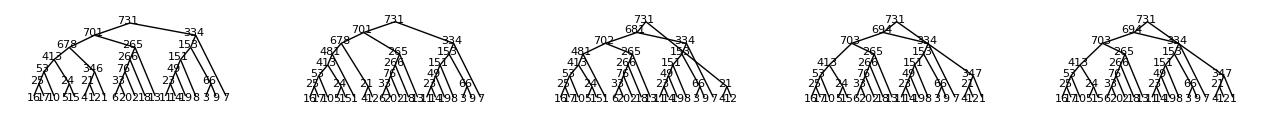

```mathematica
GraphicsRow[PlotGenealogy/@genB20[[191;;195]]]
```

As a check, the top row derives the coalescence times, by finding when the number of ancestors drops by 1, in a coalescence event.  This corresponds to the second row, na1, which derives the coalescence times from the genealogy directly:

```mathematica
na=Length[DeleteCases[#,{}]]&/@aa;
nat=Table[Length[Select[na,#>i&]],{i,1,19}]
```

{4047,339,315,248,118,86,70,66,51,43,28,25,17,15,13,9,6,5,3}

```mathematica
na1=Reverse[Sort[DeleteCases[First/@Cases[genB20[[193]],{x_Integer,{}},All],0]]]
```

{4048,340,316,249,119,87,71,67,52,44,29,26,18,16,14,10,7,6,4}

#### ancestry, genotype, addGenotype, addOutgroup, ancestralGenotypes

```mathematica
ancestry::usage="ancestry[pop,r] stores the ancestry of all the ancestors at r. ancestry[pop,{r_0,r_1},R] just uses the midpoint of the interval, provided it is valid. This structure has the same form as sweepB20, but just codes the ancestry at the specified position.";
ancestry::badInterval="Interval `1` is not valid";
ancestry[pop_List,r_?NumberQ]:=ancestry[pop,r]=Map[#[[3,1+pos[#[[2]],r]]]&,pop,{2}];
ancestry[pop_List,{r0_,r1_},R_]:=If[validIntervalQ[junctions[pop,R],{r0,r1}],
ancestry[pop,(r0+r1)/2],
Message[ancestry::badinterval,{r0,r1}];$Failed];
```

```mathematica
genotype::usage="genotype[pop,n,b,t,{r_0,r_1},R] gives the genotypes of the ancestor at this coalescence event, in this interval. Used by addGenotype";
genotype[pop_List,n_Integer,b_Integer,t_Integer,int_,R_]:=Module[{anc=ancestry[pop,int,R],ps,bl=branchListFull[pop,R]},
If[b>Length[bl],
ps=Position[anc[[t]],Range[n]];
pop[[t,ps[[1,1]],1]],
If[t==0,1,
ps=Position[anc[[t]],bl[[b,1]]][[1,1]];
pop[[t,ps,1]]]]];
```

```mathematica
addGenotype::usage="addGenotype[g,pop,n,{r_0,r_1},R] uses genotype[] to add the genotype at the selected locus to the third element of the information list. ";
addGenotype[g_Node,pop_List,n_Integer,int:{_,_},R_]:=g//.{Node[b_,{t_,{}},desc_List]:>Node[b,{t,{},genotype[pop,n,b,t,int,R]},desc]};
```

```mathematica
addOutgroup::usage="addOutgroup[g,info] adds an outgroup, with given information list, and rooted at time T (greater than any of the times in the given genealogy), and numbered as one greater than the given root. The information list is inf. The outgroup is labelled 0.";
addOutgroup::badTime="The time of divergence `1` should be greater than the root of the ingroup, `2`";
addOutgroup[g_Node,info_List]:=
If[info[[1]]≤g[[2,1]],Message[addOutgroup::badTime,info[[1]],g[[2,1]]];$Failed,
Node[g[[1]]+1,info,{Node[0,{0,{},0},{}],g}]];
```

```mathematica
ancestralGenotypes::usage="ancestralGenotypes[pop,b,{r_0,r_1},R] gives the ancestral genotypes at this location for branch # b. If the branch is not present, returns {}.";
ancestralGenotypes[pop_List,b_Integer,int:{_,_},R_]:=ancestralGenotypes[pop,b,int,R]=Module[{ps,anc},
anc=ancestry[pop,int,R];
ps=Position[anc,branchListFull[pop,R][[b,1]]];
Extract[pop,Append[#,1]]&/@ps];
```

#### validIntervalQ

```mathematica
validIntervalQ::usage="validIntervalQ[{j_1,j_2,…},{r_0,r_1}] checks that the interval does not contain any of the jucnctions. validIntervalQ[pop,{r_0,r_1},R] generates junctions using junctions[pop,R]";
validIntervalQ[jl_List,{r0_,r1_}]:=Not[Or@@((r0<#<r1)&/@jl)];
validIntervalQ[pop_List,intv:{_,_},R_]:=validIntervalQ[junctions[pop,R],intv];
```

#### updateGenealogy

```mathematica
updateGenealogy::usage="updateGenealogy[{Node[…],…},b,{d_1,…}] makes a new list of Node[…], deleting the descendant nodes d_i, and adding a new coalesced node that contains them, of the form Npde[b,{t,{}},{. The coalescence time is t.";
updateGenealogy[g:{__Node},b_Integer,d:{__Integer},t_]:=Module[{patt=Node[Alternatives@@d,_List,_List]},
Prepend[DeleteCases[g,patt],Node[b,{t,{}},Cases[g,patt]]]];
```

#### genFunction

```mathematica
genFunction::usage="genFunction[f,x,{g_1,…},{r_(1, 0),r_(1, 1)},…}] generates a piecewise function that gives f at each point x on the genome, where f is a function of the local genealogy. Requires a list of the genealogies and of the intervals. Note that x is a variable giving the location on the genome.";
genFunction[f_,x_,g_List,ints_List]:=Piecewise[Transpose[{f/@g,Between[x,#]&/@ints}]];
```

### Plotting the ARG

#### plotBranch, plotBlock

```mathematica
plotBranch::usage="plotBranch[{2,13},col,{{{X,…},..},..},R] plots blocks on {{0,R},{0,T}}, with the specified colour.";
plotBranch[br_,col_,pop_List,R_]:=Graphics[Join[{col},posBlock[pop,br,R]/.{t_Integer,{r0_,r1_}}:>Rectangle[{r0, (t-1)},{r1, t}]]];
```

```mathematica
plotBlock::usage="plotBlock[{2,13},col,{{{X,…},..},..},R] plots blocks on {{0,R},{1,N}}, with the specified colour.";
plotBlock[br_,col_,pop_List,R_]:=Module[{pb=posBlock[pop,br,R]},
Graphics[Join[{col},Outer[Rectangle[{#2[[1]], (#1-1)},{#2[[2]], #1}]&,br,pb⟦All,2⟧,1]]]];
```

#### plotBranchFull, plotBlockFull

```mathematica
plotBranchFull::usage="plotBranchFull[{{2,13},t,{{r_1,r_2}},col,{{{X,…},..},..},R] plots blocks on {{0,R},{0,T}}, with the specified colour.";
plotBranchFull[br:{_List,_Integer,_List},col_,pop_List,R_]:=Graphics[Join[{col},posBlockFull[pop,br,R]/.{t_Integer,{r0_,r1_}}:>Rectangle[{r0, (t-1)},{r1, t}]]];
```

```mathematica
plotBlockFull::usage="plotBlockFull[{{2,13},t,{{r_1,r_2}},col,{{{X,…},..},..},R] plots blocks on {{0,R},{1,N}}, with the specified colour.";
plotBlockFull[br:{_List,_Integer,_List},col_,pop_List,R_]:=Module[{pb=posBlockFull[pop,br,R]},
Graphics[Join[{col},Outer[Rectangle[{#2[[1]], (#1-1)},{#2[[2]], #1}]&,br[[1]],pb⟦All,2⟧,1]]]];
```

#### plotSNP, plotGenomes

```mathematica
plotGenomes::usage="plotGenomes[n,R] plots horizontal lines at heights 1…n, from 0 to R.";
plotGenomes[n_Integer,R_]:=Line[{{0,#},{R,#}}]&/@Range[n];
```

```mathematica
plotSNP::usage="plotSNP[k,pop] takes an array of SNP, in the form {{{t,x,k},…},…}, and generates points representing the locations on the genomes for the specified branch, k. plotSNP[{c_1,…},pop] plots all the branches according to the specified colours. plotSNP[{k,…},{c_1,…},pop] plots a subset. plotSNP[{c_1,…},ps,pop] alters point size";
plotSNP[k_Integer,pop_List]:=Module[{j},
Point[Flatten[Table[{#⟦2⟧,j}&/@Select[pop⟦j⟧,#⟦3⟧==k&],{j,Length[pop]}],1]]];
plotSNP[kl_List,c_List,pop_List]:={c[[#]],plotSNP[#,pop]}&/@kl;
plotSNP[c_List,pop_List]:=plotSNP[Range[Length[c]],c,pop];
plotSNP[kl_List,c_List,ps_,pop_List]:={c[[#]],PointSize[ps],plotSNP[#,pop]}&/@kl;
plotSNP[c_List,ps_,pop_List]:=plotSNP[Range[Length[c]],c,ps,pop];
```

#### mosaicLine, mosaicBranch

```mathematica
mosaicLine::usage="mosaicLine[{{x_0,y_0},{x_1,y_1}},{{Black},{Red}},{0,0,0,1,1,1,…}] returns {Black,Line[…],Red,Line[...],...}, representing a line coloured black or red according to the genotype list.";
mosaicLine[{xy0:{_,_},xy1:{_,_}},{c0_List,c1_List},gl_List]:=
Module[{bs=bounds[gl],cl,nb},
nb=bs[[-1,-1]];If[nb==1,bs={{0,1}},bs=(bs-1)/(nb-1)];
cl=Take[Flatten[ConstantArray[If[gl[[1]]==0,{c0,c1},{c1,c0}],Ceiling[Length[bs]/2]],1],Length[bs]];
Flatten[MapThread[Append,{cl,Line[{xy0 (1-#[[1]])+xy1 (#[[1]]),xy0 (1-#[[2]])+xy1 (#[[2]])}]&/@bs}],1]];
```

```mathematica
mosaicBranch::usage="mosaicBranch[g,pop,{r_0,r_1},R,{c_0,c_1}][{j_a,j_d}] is a function that can be applied to a pair of ancestral and descendant nodes, to give a line coloured according to ancestral genotype. It can be supplied to PlotGenealogy via BranchGraphic->mosaicBranch[]. The x coordinate in the plot is from the last element of the information list, as generated by MakeGenealogyPlot, BUT the y coordinate is taken directly from the first element. ";
mosaicBranch[mg_Node,pop_List,int_List,R_,{c0_,c1_}][{a_Integer,d_Integer}]:=
Module[{xA,xD,yA,yD},
xA=ExtractInformation[mg,a][[-1,1]];xD=ExtractInformation[mg,d][[-1,1]];
yA=ExtractInformation[mg,a][[1]];yD=ExtractInformation[mg,d][[1]];
mosaicLine[{{xD,yD},{xA,yA}},{c0,c1},ancestralGenotypes[pop,d,int,R]]];
```

#### plotCoords. plotLogCoords, plotBranchStyle

```mathematica
plotBranchStyle::usage="plotBranchStyle[{c_0},{c_1}] is a function which can be used by PlotGenealogy to style branches according to the ancestral genotype, coded in entry 3 of the information list - for example, PlotGenealogy[g,BranchStyle->plotBranchStyle[{Black},{Red}] ";
plotBranchStyle[c0_List,c1_List][_,b_List]:=If[b[[3]]==0,c0,c1];
```

```mathematica
plotLogCoords::usage="plotLogCoords[a,s] is a function which can be used by PlotGenealogy to scale to a+s*log[10,t+1] - for example, PlotGenealogy[g,NodeFunction->plotLogCoords[0,2] ";
plotLogCoords[a_,s_][_,b_List]:={b⟦-1,1⟧,a+s Log[10,1+b⟦1⟧]};
```

```mathematica
plotCoords::usage="plotCoords[s] is a function which can be used by PlotGenealogy to scale the y coordinate  by a factor s - for example, PlotGenealogy[g,NodeFunction->plotCoords[2] ";
plotCoords[y_][_,b_List]:={b⟦-1,1⟧,y b⟦1⟧};
```

### Approximating probabilities of coalescence

#### probCoal, probCoalApprox

```mathematica
probCoal::usage="probCoal[{p_0,…},r/s] approximates the probability of coalescence during the sweep. ";
probCoal[p_List,ρ_]:=Module[{interp,x},
interp=Interpolation[Mean/@GatherBy[Transpose[{p,(p[[1]]/(1-p[[1]])(1-p)/p)^(2ρ)}],#[[1]]]];
NIntegrate[interp[x],{x,Min[p],Max[p]}]];
```

```mathematica
probCoalApprox::usage="probCoalApprox[p_0,r/s] gives the probability of coalescence, assuming logistic increase from p_0. probCoalApprox[p_0,r/s,Approximate->True] gives the cruder approximation 1-p_0^(2  r/s)";
probCoalApprox[p0_,ρ_]:=(1-p0) p0 Gamma[1+2 ρ] Hypergeometric2F1Regularized[1,2,2+2 ρ,1-p0];
probCoalApprox[p0_,ρ_,Approximate->True]:=p0^(2ρ);
```

Finding the right approximation for the hitch-hiking effect, conditional on the actual trajectory, is tricky.  The expression below, derived assuming logistic increase from p_0, evaluates to essentially the same value for any trajectory p[t]; it implicitly assumes increase as ∂_t p=spq.  Its value depends only on p_0 which is 1/2N for all trajectories, and so gives the same value - but one that differs from setting p_0=1/(4Ns) as a correction for the stochastic acceleration.

f_PP=∫_p_0^1 ((p_0 q)/(q_0 p))^(2r/s)ⅆp = (1-u_0)∫_p_0^1 ((p_0 q)/(q_0 p))^(2r/s)dp/dt ⅆt

The derivation for a given trajectory should be that, working backwards, there is a probability of coalescence 1/(2Np) and a probability of escape (1-r)^2.  Therefore the probability is:

f_t=1-∏_(t=0)^∞ (1-(1-r)^2 1/(2N p_t))

For small Ns, these approximations are not very good; we need to trace the full recursions.

### Identity by descent in a selective sweep

This code is from Barton (1998, Genet. Res.), and finds the probabilities of pairwise identity, conditional on a sweep

#### probSurv

```mathematica
probSurv::usage="probSurv[{1,…},r] gives {0,…,1}, the probability of surviving both recombination and coalescence at each time";
probSurv[k_List,r_]:=Reverse[FoldList[#1(1-r)^2(1-1/#2)&,1,Reverse[k]]];
```

#### probCoal

```mathematica
probCoal::usage="probCoal[{1,…},r] sums probSurv*(1/k), to give the net probability of coalescence";
probCoal[k_List,r_]:=Total[Drop[probSurv[k,r],1]/k];
```

#### makeF, iterF

```mathematica
makeF::usage="makeF[{1,…},2N,r,μ] traces {f_QQ,f_PQ,f_PP} back in time. makeF[{1,…},r,μ] gives the identity using the old recursion, which traces forwards in time. ";
makeF[kl_List,r_]:=makeF[kl,r,0];makeF[kl_List,n_Integer,r_]=makeF[kl,n,r,0];
makeF[kl_List,r_,μ_]:=FoldList[(#1(1-r)^2(1-1/#2)+1/#2)(1-μ)^2&,1.,Drop[kl,1]];
makeF[kl_List,n_Integer,r_,μ_]:=FoldList[iterF[r,μ,n],{0,0,1.},Drop[Drop[kl,1],-1]];
```

```mathematica
iterF::usage="iterF[r,μ,2N][{f_QQ,f_PQ,f_PP},k] iterates IBD forwards in time";
iterF[r_,μ_,n_Integer][{fqq_,fpq_,fpp_},k_]:=Module[{p=k/n,q=1-k/n},
{{(1-rp)^2, 2rp(1-rp), (rp)^2}, {(1-rp)rq, ((1-rp)(1-rq)+r^2 pq), rp(1-rq)}, {(rq)^2, 2rq(1-rq), (1-rq)^2}}.{fqq(1-1/(n-k))+1/(n-k),fpq,fpp(1-1/k)+1/k}(1-μ)^2];
```

In “Hitch-hiking revisited” I sort out a confusion between Brian’s new recursion & my old one. They are both correct, but just work in different directions through time.

```mathematica
makeFold::usage="makeFold[{1,…},r] gives the identity using the old recursion, which traces forwards in time. makeF[{1,…},2N,r] traces {f_QQ,f_PQ,f_PP} forwards in time. Superseded";
makeFold[kl_List,r_]:=FoldList[(#1(1-r)^2(1-1/#2)+1/#2)&,1.,Drop[kl,1]];
makeFold[kl_List,n_Integer,r_]:=FoldList[iterFold[r,n],{0,0,1.},Drop[Drop[kl,1],-1]];
```

```mathematica
iterFold::usage="iterF[r,2N][{f_QQ,f_PQ,f_PP},k] iterates IBD forwards in time. Superseded";
iterFold[r_,n_Integer][{fqq_,fpq_,fpp_},k_]:=Module[{p=k/n,q=1-k/n},
{{(1-rp)^2, 2rp(1-rp), (rp)^2}, {(1-rp)rq, ((1-rp)(1-rq)+r^2 pq), rp(1-rq)}, {(rq)^2, 2rq(1-rq), (1-rq)^2}}.{fqq(1-1/(n-k))+1/(n-k),fpq,fpp(1-1/k)+1/k}];
```

#### h[ρ]

```mathematica
h::usage="h[ρ] gives the net identity when there are k copies, as h[ρ] (ks).  Found by interpolation in 0<ρ<1.";
h=Interpolation[{{0,1},{0.1,1.102},{0.2,1.253},{0.5,2.170},{0.7,3.52},{1,8.333}}];
```

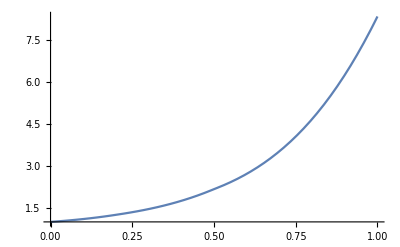

```mathematica
Plot[h[ρ],{ρ,0,1}]
```

#### soln

```mathematica
soln::usage="soln[Ns,ρ,{t_0,t_1}] solves the deterministic recursions for the identities, {fqq,fpq,fpp}. Appropriate for large r.";
soln[Ns_,ρ_,{t0_,t1_}]:=Module[{p},
p[t_]:=1/(1+ⅇ^-t);
NDSolve[{
fqq'[t]==2ρ p[t] (fpq[t]-fqq[t])+(1-fqq[t])/(2Ns (1-p[t])),
fpq'[t]==ρ( (1-p[t])fqq[t]-fpq[t]+p[t]fpp[t]),
fpp'[t]==2ρ(1-p[t]) (fpq[t]-fpp[t])+(1-fpp[t])/(2Ns p[t]),
fqq[t0]==0,fpq[t0]==0,fpp[t0]==0},{fqq,fpq,fpp},{t,t0,t1}]];
```

#### solnApprox

```mathematica
solnApprox::usage="solnApprox[ρ,{t_0,t_1}] solves the deterministic recursions for the scaled identities, {gqq, gpq, gpp}, in the limit of large Ns, when f<<1. Scaled relative to 2Ns. Appropriate for large r.";
solnApprox[ρ_,{t0_,t1_}]:=Module[{p},
p[t_]:=1/(1+ⅇ^-t);
NDSolve[{
gqq'[t]==2ρ p[t] (gpq[t]-gqq[t])+1/(1-p[t]),
gpq'[t]==ρ( (1-p[t])gqq[t]-gpq[t]+p[t]gpp[t]),
gpp'[t]==2ρ(1-p[t]) (gpq[t]-gpp[t])+1/p[t],
gqq[t0]==0,gpq[t0]==0,gpp[t0]==0},{gqq,gpq,gpp},{t,t0,t1}]⟦1⟧];
```

#### solnTr

```mathematica
solnTr::usage="solnTr[ρ,{t_0,t_1}] solves the deterministic recursions for the scaled identities, {g,Δ,δ}}, in the limit of large Ns, when f<<1. Scaled relative to 2Ns. Appropriate for large r.";
solnTr[ρ_,{t0_,t1_}]:=Module[{p},
p[t_]:=1/(1+ⅇ^-t);pq[t_]:=p[t](1-p[t]);
NDSolve[{
g'[t]==2pq[t](2p[t]-1)Δ[t]+(2pq[t])^2 δ[t]+1,
Δ'[t]==-ρ(1+4pq[t]) Δ[t]+pq[t](1+2ρ(2p[t]-1))δ[t]+2,
δ'[t]==2ρ(2p[t]-1)Δ[t]-2ρ(1-2pq[t])δ[t]+(1-2p[t])/pq[t],
g[t0]==0,δ[t0]==0,Δ[t0]==0},{g,δ,Δ},{t,t0,t1}]⟦1⟧];
```

#### makeFamilies

```mathematica
makeFamilies::usage="makeFamilies[{1,…,2N},r,2N,J] iterates back the ancestry of J genes, returning the family structure.";
makeFamilies[kl_List,r_,n_,j_Integer]:=Fold[iterBack[#1,r,n,#2]&,{{},List/@Range[j]},Reverse[kl]];
```

### General utilities

#### findT

```mathematica
findT::usage="findT[{1,…},k^*] finds the time at which k_t first exceeds k^*";
findT[s_List,k_]:=First[Pick[Range[Length[s]],(#>k)&/@s]];
```

#### pos, bounds, int

```mathematica
pos::usage="pos[{j_1,j_2,…},x] gives the position of the largest j_i smaller than x, or 0 if x<j_1";
pos[jl_List,x_]:=Module[{jl1=Append[jl,∞]},
FirstPosition[jl1,SelectFirst[jl1,(#>x)&]]⟦1⟧-1];
Protect[pos];
```

```mathematica
bounds::usage="bounds[{0,0,1,1,1,0,...}] uses Split to group consecutive elements, and retunrs the first and last elements of each, in the form {{1,2},{3,5},…}";
bounds[y_List]:=Module[{fl},fl=FoldList[Plus,1,Length/@Split[y]];
Transpose[{Drop[fl,-1],Drop[fl,1]-1}]];
```

```mathematica
int::usage="int[1,{r_1,…},R] gives the interval {0,r_1}";
int[k_Integer,r_List,R_]:=Append[Prepend[r,0],R][[{k,k+1}]];
Protect[int];
```

#### randomSet

```mathematica
randomSet::usage="randomSet[n,k] chooses n parents from 1…k, and returns the sizes of sibling families larger than 1";
randomSet[n_Integer,k_Integer]:=Last/@DeleteCases[Sort[Tally[RandomInteger[{1,k},n]]],{_,1}];
```